# Textually Describing Wolfram Language Expressions

Renan Germano

Mackenzie Presbyterian University

The objective of the present project is to create a function to textually describe Wolfram Language expressions. This is done by developing an algorithm that is capable of better describing the input, based on its symbolic structure, where the output is a human readable String. Thinking about accessibility for visually impaired, this text could be used as an automatically generated alternative description for graphics and related content.

## Wolfram Community Post (material for blog post)

## Complete project work

### Manipulating Wolfram Language symbols

```mathematica
WolframLanguageData["List", "Properties"]
```

{attributes,character count,common option values,date introduced,date last modified,dates modified,documentation basic examples,documentation example counts,documentation example inputs,documentation example text,entity classes,eponymous people,equal-precedence symbols,external links,frequencies of usage,full version introduced,full version last modified,full versions modified,functionality areas,symbol background,keyboard shortcuts,link trails,memberships,name,option names,options,plaintext usage,precedence ranks,ranks of usage,related entities,related guide pages,related symbols,relationship community graph,relationship graph,short notations,subject classifications,symbols linking to,symbols using as attribute,symbols using as option,text strings,timeline,timeline events,translations,typeset usage,URL,version introduced,version last modified,versions modified,Wolfram documentation link}

```mathematica
?WolframLanguageData
```

```mathematica
wlSymbols=WolframLanguageData[];
```

```mathematica
wlSymbols//Length
```

5605

```mathematica
wlEntityProperties=WolframLanguageData["Properties"]
```

{attributes,character count,common option values,date introduced,date last modified,dates modified,documentation basic examples,documentation example counts,documentation example inputs,documentation example text,entity classes,eponymous people,equal-precedence symbols,external links,frequencies of usage,full version introduced,full version last modified,full versions modified,functionality areas,symbol background,keyboard shortcuts,link trails,memberships,name,option names,options,plaintext usage,precedence ranks,ranks of usage,related entities,related guide pages,related symbols,relationship community graph,relationship graph,short notations,subject classifications,symbols linking to,symbols using as attribute,symbols using as option,text strings,timeline,timeline events,translations,typeset usage,URL,version introduced,version last modified,versions modified,Wolfram documentation link}

```mathematica
functionalityAreasOfAllWLSymbols=MapThread[{#1,#2}&,{wlSymbols,EntityValue[wlSymbols,EntityProperty["WolframLanguageSymbol","FunctionalityAreas"]]}];
```

```mathematica
AllPropertiesForSymbol[symbol_Symbol]:=EntityValue[WolframLanguageData@ToString@symbol,wlEntityProperties]
```

```mathematica
RelationshipGraphs[symbol_Symbol]:=EntityValue[WolframLanguageData@ToString@symbol,{EntityProperty["WolframLanguageSymbol","RelationshipGraph"],EntityProperty["WolframLanguageSymbol","RelationshipCommunityGraph"]}]
```

### Already build-in functions to describe Wolfram Language expressions

```mathematica
redSphere=Graphics3D[{Red,Sphere[]}]
```

-Graphics3D-

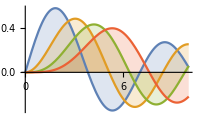

```mathematica
complexGraph=Plot[Evaluate[Table[BesselJ[n,x],{n,4}]],{x,0,10},Filling->Axis]
```

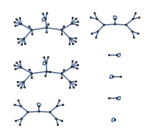

```mathematica
someGraphs=GraphPlot[Table[i->Mod[i^2,102],{i,0,102}]]
```

#### SpokenString

```mathematica
?SpokenString
SpokenString@redSphere
SpokenString@complexGraph
SpokenString@someGraphs
```

a three-dimensional graphic consisting of a sphere

a graphic consisting of 11 polygons, a line connecting 574 points, a line connecting 541 points, a line connecting 556 points and a line connecting 610 points

a graphic consisting of 103 arrows and 103 disks

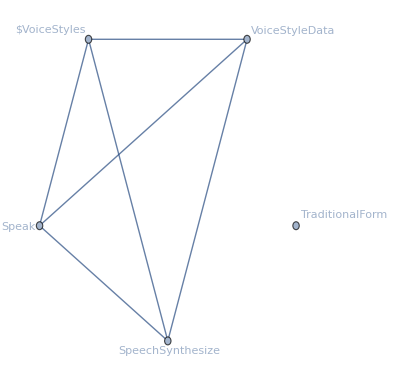
{-Graphics-,-Graphics-}

```mathematica
RelationshipGraphs@SpokenString
```

#### TextString

```mathematica
?TextString
TextString@redSphere
TextString@complexGraph
TextString@someGraphs
```

redSphere

complexGraph

someGraphs

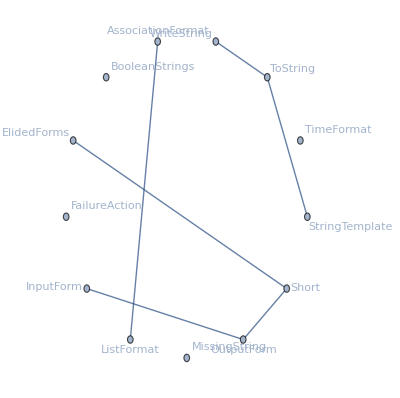
{-Graphics-,-Graphics-}

```mathematica
RelationshipGraphs@TextString
```

#### ToString

```mathematica
?ToString
ToString@redSphere
ToString@complexGraph
ToString@someGraphs
```

redSphere

complexGraph

someGraphs

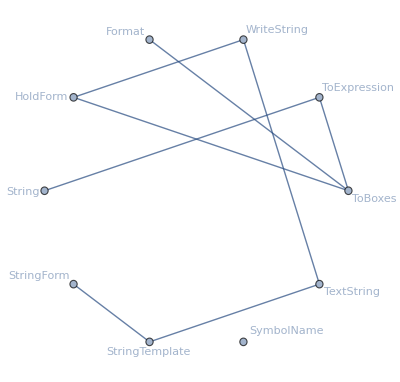
{-Graphics-,-Graphics-}

```mathematica
RelationshipGraphs@ToString
```

#### Description and TranslatedDescription functions for symbols

```mathematica
Clear@Description
```

```mathematica
Description[symbol_Symbol]:=With[
{entity=Entity["WolframLanguageSymbol",ToString@symbol]},
Description[symbol]=entity@"Name"
]

SetAttributes[Description,Listable]
```

```mathematica
Clear@TranslatedDescription
```

```mathematica
TranslatedDescription[symbol_Symbol,language_String]:=Block[
{entity,lang,translations},
entity=Entity["WolframLanguageSymbol",ToString@symbol];
lang=Entity["Language",language];
translations=Association[entity@"Translations"];
TranslatedDescription[symbol,language]=translations@lang
]
TranslatedDescription[symbol_Symbol]:=Description[symbol]

SetAttributes[TranslatedDescription,Listable]
```

Some tests

```mathematica
someWLSymbols={List,Table,Range,Graphics,Image,ColorQ,Number,Grid,Entity,Values,Map,Thread,Function}
```

{List,Table,Range,Graphics,Image,ColorQ,Number,Grid,Entity,Values,Map,Thread,Function}

```mathematica
Head/@someWLSymbols
```

{Symbol,Symbol,Symbol,Symbol,Symbol,Symbol,Symbol,Symbol,Symbol,Symbol,Symbol,Symbol,Symbol}

```mathematica
symbolDescriptionTests=Module[
{descriptions=Description@someWLSymbols,spanish,portuguese,japanese},
spanish=TranslatedDescription[someWLSymbols,"Spanish"];
portuguese=TranslatedDescription[someWLSymbols,"Portuguese"];
japanese=TranslatedDescription[someWLSymbols,"Japanese"];
MapThread[{#1,#2,#3,#4,#5}&,{someWLSymbols,descriptions,spanish,portuguese,japanese}]
];
```

```mathematica
Grid[symbolDescriptionTests,Frame->All]
```

List | List | lista | lista | リスト
Table | Table | tabla | tabela | リストを作成
Range | Range | rango | intervalo de valores | 範囲
Graphics | Graphics | gráfico | representação gráfica | グラフィックス
Image | Image | imagen | imagem | 画像
ColorQ | ColorQ | ¿color? | Cor? | 色かどうか
Number | Number | número | número | 数
Grid | Grid | rejilla | grade | 格子
Entity | Entity | entidad | entidade | 実体
Values | Values | valores | lista de valores de associação | 値
Map | Map | aplica a todos | aplica-se ao primeiro nível | 適用
Thread | Thread | atraviesa | através das listas | 縫い込む
Function | Function | función | função | 関数

#### A parenthesis: the PrintDefinitions function

PrintDefinitions, a function from the Wolfram Function repository, creates a notebook object for a WL symbol, containing the symbol documentation/definition content.

```mathematica
ResourceFunction["PrintDefinitions"]
```

```mathematica
PrintDefinitions@Graphics
```

yghv2_shm184FrontEndObject[LinkObject["yghv2_shm", 3, 1]]184System`Graphics

### Describing Colors

#### Named Colors

```mathematica
redNamedColorWLEntity=WolframLanguageData["Red"]
```

Red

```mathematica
entityPropertyValuesForRedColor={#,EntityValue[redNamedColorWLEntity, #]}&/@wlEntityProperties;
```

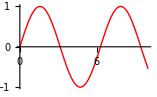
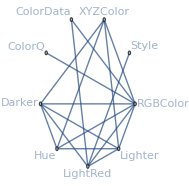
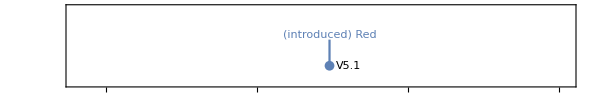
attributes | {Protected}
character count | 3
date introduced | Day: Mon 25 Oct 2004
documentation basic examples | {{Graphics[{Red,Disk[]}],-Graphics-,Plot[Sin[x],{x,0,10},PlotStyle→Red],-Graphics-,Graphics3D[{Red,Sphere[]}],-Graphics3D-}}
documentation example counts | {BasicExamples→1,Scope→0,GeneralizationsExtensions→0,Options→0,Applications→0,PropertiesRelations→0,PossibleIssues→0,InteractiveExamples→0,NeatExamples→0}
documentation example inputs | {BasicExamples→{{Graphics[{Red,Disk[]}],Plot[Sin[x],{x,0,10},PlotStyle→Red],Graphics3D[{Red,Sphere[]}]}},Scope→{},GeneralizationsExtensions→{},Options→{},Applications→{},PropertiesRelations→{},PossibleIssues→{},InteractiveExamples→{},NeatExamples→{}}
documentation example text | {BasicExamples→{{}},Scope→{},GeneralizationsExtensions→{},Options→{},Applications→{},PropertiesRelations→{},PossibleIssues→{},InteractiveExamples→{},NeatExamples→{}}
entity classes | {Wolfram Language autoevaluating symbols}
eponymous people | {}
external links | {}
frequencies of usage | {All→0.000434382,StackExchange→0.00233259,TypicalProductionCode→0.0010278,WolframAlphaCodebase→0.0000142108,WolframDemonstrations→0.00218411,WolframDocumentation→0.00162619}
full version introduced | 5.1
functionality areas | {ColorSymbols}
symbol background | Red is a symbol that represents the color red in graphics or style specifications. Color specifications in the Wolfram Language can appear explicitly inside a Graphics or Graphics3D expression (e.g. Graphics[{Red,Disk[]}]), in which case they affect all subsequent expressions until another specification overrides them. They can also be used as part of an option specification, either singly (e.g. Plot[Sin[x],{x,0,2Pi},PlotStyle->Red]) or as part of a Directive compound expression (e.g. Plot[Cos[x],{x,0,2Pi},PlotStyle->Directive[Thick,Red]]). Finally, they can appear inside Style wrappers that affect the appearance of text, equations, and notebook cells (e.g. Style[hello,Red]).
Red is a color located at one of the corners of the RGB color cube and evaluates to RGBColor[1,0,0].
Named symbols for other colors include Green, Blue, Black, White, Gray, Cyan, Magenta, Yellow, Brown, Orange, Pink, and Purple, as well as their LightRed etc. variants. Arbitrary colors can be input using Hue, RGBColor, CMYKColor, LABColor, LUVColor, or XYZColor. Colors can be modified using Lighter, Darker, and Blend. Colors may be converted between different systems using ColorConvert. The appearance of colors appearing in Graphics3D objects may be controlled using Glow, Specularity, and Lighting. The transparency of colored graphics objectives can be specified using Opacity. ColorData can be used to give a function that generates colors in a named color scheme.
link trails | {{guide/WolframRoot,guide/ColorProcessing,guide/Colors,ref/Red},{guide/WolframRoot,guide/GraphicsOptionsAndStyling,guide/Colors,ref/Red},{guide/WolframRoot,guide/DataVisualization,guide/ColorProcessing,guide/Colors,ref/Red},{guide/WolframRoot,guide/ImageProcessing,guide/ColorProcessing,guide/Colors,ref/Red},{guide/WolframRoot,guide/SymbolicGraphicsLanguage,guide/GraphicsDirectives,guide/Colors,ref/Red},{guide/WolframRoot,guide/FinancialVisualization,guide/DataVisualization,guide/ColorProcessing,guide/Colors,ref/Red},{guide/WolframRoot,guide/MapsAndCartography,guide/SymbolicGraphicsLanguage,guide/GraphicsDirectives,guide/Colors,ref/Red},{guide/WolframRoot,guide/ScientificDataAnalysis,guide/DataVisualization,guide/ColorProcessing,guide/Colors,ref/Red},{guide/WolframRoot,guide/ScientificDataAnalysis,guide/ImageProcessing,guide/ColorProcessing,guide/Colors,ref/Red},{guide/WolframRoot,guide/ChartingAndInformationVisualization,guide/FinancialVisualization,guide/DataVisualization,guide/ColorProcessing,guide/Colors,ref/Red},{guide/WolframRoot,guide/ChartingAndInformationVisualization,guide/StatisticalVisualization,guide/DataVisualization,guide/ColorProcessing,guide/Colors,ref/Red},{guide/WolframRoot,guide/DateAndTime,guide/FinancialVisualization,guide/DataVisualization,guide/ColorProcessing,guide/Colors,ref/Red},{guide/WolframRoot,guide/Finance,guide/FinancialVisualization,guide/DataVisualization,guide/ColorProcessing,guide/Colors,ref/Red},{guide/WolframRoot,guide/GeographicData,guide/MapsAndCartography,guide/SymbolicGraphicsLanguage,guide/GraphicsDirectives,guide/Colors,ref/Red},{guide/WolframRoot,guide/GeometricComputation,guide/Polygons,guide/SymbolicGraphicsLanguage,guide/GraphicsDirectives,guide/Colors,ref/Red},{guide/WolframRoot,guide/GeometricComputation,guide/Polyhedra,guide/SymbolicGraphicsLanguage,guide/GraphicsDirectives,guide/Colors,ref/Red},{guide/WolframRoot,guide/LocationsPathsAndRouting,guide/MapsAndCartography,guide/SymbolicGraphicsLanguage,guide/GraphicsDirectives,guide/Colors,ref/Red},{guide/WolframRoot,guide/Statistics,guide/StatisticalVisualization,guide/DataVisualization,guide/ColorProcessing,guide/Colors,ref/Red},{guide/WolframRoot,guide/3DPrinting,guide/GeometricComputation,guide/Polygons,guide/SymbolicGraphicsLanguage,guide/GraphicsDirectives,guide/Colors,ref/Red},{guide/WolframRoot,guide/3DPrinting,guide/GeometricComputation,guide/Polyhedra,guide/SymbolicGraphicsLanguage,guide/GraphicsDirectives,guide/Colors,ref/Red},{guide/WolframRoot,guide/ActuarialComputation,guide/Finance,guide/FinancialVisualization,guide/DataVisualization,guide/ColorProcessing,guide/Colors,ref/Red},{guide/WolframRoot,guide/ActuarialComputation,guide/RandomVariables,guide/StatisticalVisualization,guide/DataVisualization,guide/ColorProcessing,guide/Colors,ref/Red},{guide/WolframRoot,guide/Calculus,guide/GeometricComputation,guide/Polygons,guide/SymbolicGraphicsLanguage,guide/GraphicsDirectives,guide/Colors,ref/Red},{guide/WolframRoot,guide/Calculus,guide/GeometricComputation,guide/Polyhedra,guide/SymbolicGraphicsLanguage,guide/GraphicsDirectives,guide/Colors,ref/Red},{guide/WolframRoot,guide/DateAndTime,guide/DateAndTimeVisualization,guide/FinancialVisualization,guide/DataVisualization,guide/ColorProcessing,guide/Colors,ref/Red},{guide/WolframRoot,guide/EarthSciencesDataAndComputation,guide/GeographicData,guide/MapsAndCartography,guide/SymbolicGraphicsLanguage,guide/GraphicsDirectives,guide/Colors,ref/Red},{guide/WolframRoot,guide/Finance,guide/DateAndTime,guide/FinancialVisualization,guide/DataVisualization,guide/ColorProcessing,guide/Colors,ref/Red},{guide/WolframRoot,guide/Geodesy,guide/DateAndTime,guide/FinancialVisualization,guide/DataVisualization,guide/ColorProcessing,guide/Colors,ref/Red},{guide/WolframRoot,guide/Geodesy,guide/LocationsPathsAndRouting,guide/MapsAndCartography,guide/SymbolicGraphicsLanguage,guide/GraphicsDirectives,guide/Colors,ref/Red},{guide/WolframRoot,guide/LifeSciencesAndMedicineDataAndComputation,guide/Statistics,guide/StatisticalVisualization,guide/DataVisualization,guide/ColorProcessing,guide/Colors,ref/Red},{guide/WolframRoot,guide/PeopleAndHistory,guide/DateAndTime,guide/FinancialVisualization,guide/DataVisualization,guide/ColorProcessing,guide/Colors,ref/Red},{guide/WolframRoot,guide/PlaneGeometry,guide/GeometricComputation,guide/Polygons,guide/SymbolicGraphicsLanguage,guide/GraphicsDirectives,guide/Colors,ref/Red},{guide/WolframRoot,guide/PlaneGeometry,guide/GeometricComputation,guide/Polyhedra,guide/SymbolicGraphicsLanguage,guide/GraphicsDirectives,guide/Colors,ref/Red},{guide/WolframRoot,guide/ProbabilityAndStatistics,guide/RandomVariables,guide/StatisticalVisualization,guide/DataVisualization,guide/ColorProcessing,guide/Colors,ref/Red},{guide/WolframRoot,guide/ScientificDataAnalysis,guide/DescriptiveStatistics,guide/StatisticalVisualization,guide/DataVisualization,guide/ColorProcessing,guide/Colors,ref/Red},{guide/WolframRoot,guide/ScientificDataAnalysis,guide/RandomVariables,guide/StatisticalVisualization,guide/DataVisualization,guide/ColorProcessing,guide/Colors,ref/Red},{guide/WolframRoot,guide/ScientificDataAnalysis,guide/Statistics,guide/StatisticalVisualization,guide/DataVisualization,guide/ColorProcessing,guide/Colors,ref/Red},{guide/WolframRoot,guide/SolidGeometry,guide/GeometricComputation,guide/Polygons,guide/SymbolicGraphicsLanguage,guide/GraphicsDirectives,guide/Colors,ref/Red},{guide/WolframRoot,guide/SolidGeometry,guide/GeometricComputation,guide/Polyhedra,guide/SymbolicGraphicsLanguage,guide/GraphicsDirectives,guide/Colors,ref/Red},{guide/WolframRoot,guide/Statistics,guide/DescriptiveStatistics,guide/StatisticalVisualization,guide/DataVisualization,guide/ColorProcessing,guide/Colors,ref/Red},{guide/WolframRoot,guide/TimeSeries,guide/DateAndTime,guide/FinancialVisualization,guide/DataVisualization,guide/ColorProcessing,guide/Colors,ref/Red},{guide/WolframRoot,guide/TimeSeries,guide/DateAndTimeVisualization,guide/FinancialVisualization,guide/DataVisualization,guide/ColorProcessing,guide/Colors,ref/Red},{guide/WolframRoot,guide/TimeSeries,guide/RandomVariables,guide/StatisticalVisualization,guide/DataVisualization,guide/ColorProcessing,guide/Colors,ref/Red}}
memberships | {Wolfram Language autoevaluating symbols}
name | Red
option names | {}
options | {}
plaintext usage | Red represents the color red in graphics or style specifications.
ranks of usage | {All→91,StackExchange→41,TypicalProductionCode→87,WolframAlphaCodebase→398,WolframDemonstrations→48,WolframDocumentation→54}
related entities | {red}
related guide pages | {Colorspaclet:guide/Colors,Symbolic Graphics Languagepaclet:guide/SymbolicGraphicsLanguage,Graphics Options & Stylingpaclet:guide/GraphicsOptionsAndStyling,Graphics Annotation & Appearancepaclet:guide/GraphicsAnnotationAndAppearance,Graphics Directivespaclet:guide/GraphicsDirectives,Maps & Cartographypaclet:guide/MapsAndCartography,Color Processingpaclet:guide/ColorProcessing,Notebook Formatting & Stylingpaclet:guide/NotebookFormattingAndStyling,Chart Styling & Layoutpaclet:guide/ChartLayoutAndStyling,Graph Visualizationpaclet:guide/GraphVisualization,Text Stylingpaclet:guide/TextStyling,GeoGraphics Languagepaclet:guide/GeoGraphicsLanguage,Graph Styling, Labeling, and Layoutpaclet:guide/GraphStylingAndLabeling,Maps & Cartographypaclet:guide/MapsAndGeographicData}
related symbols | {LightRed,ColorData,Lighter,Darker,Hue,RGBColor,Style}
relationship community graph | -Graphics-
relationship graph | -Graphics-
symbols linking to | {ColorQ,Hue,LightRed,RGBColor,XYZColor}
symbols using as attribute | {}
symbols using as option | {}
text strings | {Red represents the color red in graphics or style specifications.,Red is equivalent to RGBColor[1,0,0].,Red is a symbol that represents the color red in graphics or style specifications. Color specifications in the Wolfram Language can appear explicitly inside a Graphics or Graphics3D expression (e.g. Graphics[{Red,Disk[]}]), in which case they affect all subsequent expressions until another specification overrides them. They can also be used as part of an option specification, either singly (e.g. Plot[Sin[x],{x,0,2Pi},PlotStyle->Red]) or as part of a Directive compound expression (e.g. Plot[Cos[x],{x,0,2Pi},PlotStyle->Directive[Thick,Red]]). Finally, they can appear inside Style wrappers that affect the appearance of text, equations, and notebook cells (e.g. Style["hello",Red]).,Red is a color located at one of the corners of the RGB color cube and evaluates to RGBColor[1,0,0].,Named symbols for other colors include Green, Blue, Black, White, Gray, Cyan, Magenta, Yellow, Brown, Orange, Pink, and Purple, as well as their LightRed etc. variants. Arbitrary colors can be input using Hue, RGBColor, CMYKColor, LABColor, LUVColor, or XYZColor. Colors can be modified using Lighter, Darker, and Blend. Colors may be converted between different systems using ColorConvert. The appearance of colors appearing in Graphics3D objects may be controlled using Glow, Specularity, and Lighting. The transparency of colored graphics objectives can be specified using Opacity. ColorData can be used to give a function that generates colors in a named color scheme.}
timeline | -Graphics-
timeline events | Day: Mon 25 Oct 2004Red
translations | {Simplified Chinese→红色,Traditional Chinese→紅色,French→rouge,German→rot,Modern Greek→κόκκινο,Japanese→赤,Korean→빨강,Lithuanian→raudonas,Polish→czerwony,Portuguese→vermelho,Russian→красный,Spanish→rojo,Ukrainian→червоний,Vietnamese→đỏ}
typeset usage | Red represents the color red in graphics or style specifications. 
URL | http://reference.wolfram.com/language/ref/Red.html
version introduced | 5.1
Wolfram documentation link | Redpaclet:ref/Red

```mathematica
Grid[Select[entityPropertyValuesForRedColor, Not@MissingQ@Last@#&], Frame->All]
```

```mathematica
colorSymbols=Select[functionalityAreasOfAllWLSymbols, (Length@Last@#)==1&&((First@Last@#)=="ColorSymbols")&]⟦All,1⟧
```

{Black,Blend,Blue,Brown,CMYKColor,ChromaticityPlot,ChromaticityPlot3D,ColorBalance,ColorCombine,ColorConvert,ColorCoverage,ColorData,ColorDataFunction,ColorDetect,ColorDistance,ColorFunction,ColorFunctionScaling,ColorNegate,ColorProfileData,ColorQ,ColorQuantize,ColorReplace,ColorRules,ColorSeparate,ColorSetter,ColorSpace,ColorToneMapping,Colorize,ColorsNear,Cyan,Darker,Dithering,FindMatchingColor,Glow,Gray,GrayLevel,Green,Hue,ImageColorSpace,LABColor,LCHColor,LUVColor,LightBlue,LightBrown,LightCyan,LightGray,LightGreen,LightMagenta,LightOrange,LightPink,LightPurple,LightRed,LightYellow,Lighter,Magenta,MaxColorDistance,MinColorDistance,Orange,Pink,Purple,RGBColor,RandomColor,Red,StreamColorFunction,StreamColorFunctionScaling,VectorColorFunction,VectorColorFunctionScaling,White,WhitePoint,XYZColor,Yellow}

```mathematica
namedColors= Select[colorSymbols,ColorQ@RGBColor@#["Name"]&]
```

{Black,Blue,Brown,Cyan,Gray,Green,LightBlue,LightCyan,LightGreen,LightPink,LightYellow,Magenta,Orange,Pink,Purple,Red,White,Yellow}

```mathematica
Grid[{#, RGBColor@#@"Name", #@"Name", #@"Translations"}&/@namedColors, Frame->All]
```

```mathematica
namedColorsRGB=Association[RGBColor@#@"Name"->#&/@namedColors]
```

<|RGBColor[0., 0., 0.]→Black,RGBColor[0., 0., 1.]→Blue,RGBColor[0.6470588235294118, 0.1647058823529412, 0.1647058823529412]→Brown,RGBColor[0., 1., 1.]→Cyan,RGBColor[0.5019607843137255, 0.5019607843137255, 0.5019607843137255]→Gray,RGBColor[0., 0.5019607843137255, 0.]→Green,RGBColor[0.6784313725490198, 0.847058823529412, 0.901960784313726]→LightBlue,RGBColor[0.87843137254902, 1., 1.]→LightCyan,RGBColor[0.5647058823529411, 0.933333333333333, 0.5647058823529411]→LightGreen,RGBColor[1., 0.7137254901960784, 0.7568627450980392]→LightPink,RGBColor[1., 1., 0.87843137254902]→LightYellow,RGBColor[1., 0., 1.]→Magenta,RGBColor[1., 0.6470588235294118, 0.]→Orange,RGBColor[1., 0.7529411764705882, 0.796078431372549]→Pink,RGBColor[0.5019607843137255, 0., 0.5019607843137255]→Purple,RGBColor[1., 0., 0.]→Red,RGBColor[1., 1., 1.]→White,RGBColor[1., 1., 0.]→Yellow|>

```mathematica
MyColorDistance[color1_RGBColor,color2_RGBColor]:=N[Mean[MapThread[Abs[#1-#2]&,{List@@color1,List@@color2}]]]
MyColorDistance[Red,Red]
MyColorDistance[Red,Green]
MyColorDistance[Red,Blue]
MyColorDistance[Red,Pink]
MyColorDistance[Red,Black]
```

0.

0.666667

0.666667

0.333333

MyColorDistance[RGBColor[1, 0, 0],GrayLevel[0]]

```mathematica
randomColor=RGBColor[RandomReal[1],RandomReal[1],RandomReal[1]]
nearestColor = Nearest[Keys@namedColorsRGB,randomColor,1]//First
namedColorsRGB[nearestColor]["Name"]
Association[namedColorsRGB[nearestColor]["Translations"]][Entity["Language","Portuguese"]]
```

RGBColor[0.32791526849313435, 0.4964549822940518, 0.007826250271401713]

RGBColor[0., 0.5019607843137255, 0.]

Green

verde

#### Description function for colors

```mathematica
Description[color_RGBColor]:=Block[
{colors=<|RGBColor[0., 0., 0.]->Entity["WolframLanguageSymbol","Black"],RGBColor[0., 0., 1.]->Entity["WolframLanguageSymbol","Blue"],RGBColor[0.6470588235294118, 0.1647058823529412, 0.1647058823529412]->Entity["WolframLanguageSymbol","Brown"],RGBColor[0., 1., 1.]->Entity["WolframLanguageSymbol","Cyan"],RGBColor[0.5019607843137255, 0.5019607843137255, 0.5019607843137255]->Entity["WolframLanguageSymbol","Gray"],RGBColor[0., 0.5019607843137255, 0.]->Entity["WolframLanguageSymbol","Green"],RGBColor[0.6784313725490198, 0.847058823529412, 0.901960784313726]->Entity["WolframLanguageSymbol","LightBlue"],RGBColor[0.87843137254902, 1., 1.]->Entity["WolframLanguageSymbol","LightCyan"],RGBColor[0.5647058823529411, 0.933333333333333, 0.5647058823529411]->Entity["WolframLanguageSymbol","LightGreen"],RGBColor[1., 0.7137254901960784, 0.7568627450980392]->Entity["WolframLanguageSymbol","LightPink"],RGBColor[1., 1., 0.87843137254902]->Entity["WolframLanguageSymbol","LightYellow"],RGBColor[1., 0., 1.]->Entity["WolframLanguageSymbol","Magenta"],RGBColor[1., 0.6470588235294118, 0.]->Entity["WolframLanguageSymbol","Orange"],RGBColor[1., 0.7529411764705882, 0.796078431372549]->Entity["WolframLanguageSymbol","Pink"],RGBColor[0.5019607843137255, 0., 0.5019607843137255]->Entity["WolframLanguageSymbol","Purple"],RGBColor[1., 0., 0.]->Entity["WolframLanguageSymbol","Red"],RGBColor[1., 1., 1.]->Entity["WolframLanguageSymbol","White"],RGBColor[1., 1., 0.]->Entity["WolframLanguageSymbol","Yellow"]|>,similar,entity},
similar=First@Nearest[Keys@colors,color,1];
entity=colors@similar;
Description[color]=entity@"Name"
]

SetAttributes[Description,Listable]
```

Some tests

```mathematica
randomColor=RGBColor[RandomReal[1],RandomReal[1],RandomReal[1]]
Description[randomColor]
```

RGBColor[0.253769604199354, 0.5974827503076772, 0.6504355856456245]

LightBlue

```mathematica
colorDescriptionTests={#, Style[Description@#,#]}&/@RGBColor/@RandomReal[1,{100,3}];
```

```mathematica
Grid[#,Frame->All,Alignment->Left]&/@ArrayReshape[colorDescriptionTests,{5,20,2}]
```

{RGBColor[{0.8404423493844511, 0.408963151036142, 0.29847007753518073}] | Brown
RGBColor[{0.3118181202014607, 0.5119149037182933, 0.8998829506127082}] | LightBlue
RGBColor[{0.11780182280470552, 0.18146105404024349, 0.6700171001087474}] | Purple
RGBColor[{0.43195538790514876, 0.7336969125019048, 0.2857447637047872}] | LightGreen
RGBColor[{0.6817458716893248, 0.7439478637074746, 0.4781519607099536}] | LightGreen
RGBColor[{0.5925430433015808, 0.5194050026315777, 0.8908703755714564}] | Purple
RGBColor[{0.5567167196661353, 0.790265646369446, 0.7514502355287167}] | LightBlue
RGBColor[{0.5254628238848986, 0.7562562135648856, 0.08715099746714161}] | Green
RGBColor[{0.7857351829203192, 0.43914428922410287, 0.9958498002069038}] | Purple
RGBColor[{0.5200600721599611, 0.07180956146256823, 0.35619955896094724}] | Purple
RGBColor[{0.37287768554502243, 0.5777410463739294, 0.8635668768012168}] | LightBlue
RGBColor[{0.6206322528526864, 0.8383464169003298, 0.5857974453261974}] | LightGreen
RGBColor[{0.9784961169737165, 0.16919335282017567, 0.9686377791495135}] | Magenta
RGBColor[{0.4784861812476904, 0.33479500208043844, 0.788046587610681}] | Purple
RGBColor[{0.881731334210885, 0.10409999698187833, 0.026791542286180636}] | Red
RGBColor[{0.7115802383897352, 0.8343250176481893, 0.8026706286855478}] | LightBlue
RGBColor[{0.5833847803411802, 0.4861560591635632, 0.07905845742231432}] | Orange
RGBColor[{0.2382574370158177, 0.02379698790057616, 0.964514142539765}] | Blue
RGBColor[{0.2207397142097569, 0.3432565381231514, 0.14644831641999123}] | Gray
RGBColor[{0.20588278985558328, 0.4086334114830832, 0.17159254658520173}] | Green,RGBColor[{0.1500881091826496, 0.7557120974805784, 0.8780984486544301}] | LightBlue
RGBColor[{0.36106186398886764, 0.8501930032946572, 0.5642898674644938}] | LightGreen
RGBColor[{0.023952757175419892, 0.04868960668695621, 0.3781804707280201}] | Purple
RGBColor[{0.17925131140843176, 0.5929907351664492, 0.9483481245862577}] | LightBlue
RGBColor[{0.9305768497688187, 0.29262795768605954, 0.3093053317963421}] | Brown
RGBColor[{0.7576151334311816, 0.839801099387534, 0.6730177171614924}] | LightYellow
RGBColor[{0.7671084112983704, 0.3763879191042454, 0.6025285425965381}] | Purple
RGBColor[{0.7563241609429812, 0.23762248165537692, 0.5599175725405661}] | Purple
RGBColor[{0.431449760980519, 0.7241329906771077, 0.6790767640327005}] | LightBlue
RGBColor[{0.13867520662604194, 0.9363894952526801, 0.19525296080017362}] | LightGreen
RGBColor[{0.2873346847835341, 0.9130672657857872, 0.6397652183142248}] | LightGreen
RGBColor[{0.7156451699172992, 0.06546996030648788, 0.268618824918778}] | Brown
RGBColor[{0.43008784544508827, 0.8993105102180845, 0.5442066337205949}] | LightGreen
RGBColor[{0.18336345220038996, 0.5001065733259964, 0.5072370850102599}] | Gray
RGBColor[{0.5358948630544893, 0.18349392489506977, 0.20107323974509694}] | Brown
RGBColor[{0.01985961994569374, 0.258375927860951, 0.5321072258242558}] | Purple
RGBColor[{0.46765721498674084, 0.17288678920582834, 0.6164358458311316}] | Purple
RGBColor[{0.5321740280900629, 0.6728990977716749, 0.2085950711915805}] | Green
RGBColor[{0.05259901515381027, 0.16074644356210088, 0.625065842590494}] | Purple
RGBColor[{0.14975756384717642, 0.4844604182502723, 0.7979653891359446}] | Gray,RGBColor[{0.37608852464191567, 0.9732088624690132, 0.2470960728171392}] | LightGreen
RGBColor[{0.43279237556405503, 0.33888479804213056, 0.21394634899297538}] | Gray
RGBColor[{0.5013035574388023, 0.42507751535813987, 0.8719427703440001}] | Purple
RGBColor[{0.7284077329455674, 0.9599773168973369, 0.7023388904005456}] | LightGreen
RGBColor[{0.7515082199763463, 0.43191558396813945, 0.7614487709767721}] | Purple
RGBColor[{0.915018940387782, 0.9466385643567174, 0.6726318241637526}] | LightYellow
RGBColor[{0.16920115715633033, 0.9482372338966893, 0.41370355717508533}] | LightGreen
RGBColor[{0.8126288341580337, 0.40527064366324916, 0.41713393438840973}] | Brown
RGBColor[{0.44028369737728257, 0.8831195102883282, 0.9176400630034969}] | LightBlue
RGBColor[{0.4490721484460789, 0.9071470599281153, 0.05544797590863171}] | LightGreen
RGBColor[{0.9980751217071944, 0.996124574662822, 0.7570713051828317}] | LightYellow
RGBColor[{0.7841558371762696, 0.26003914757446656, 0.42166306986230206}] | Brown
RGBColor[{0.49729516856217937, 0.4775629694752339, 0.40735672433941184}] | Gray
RGBColor[{0.1734806959200097, 0.4998659219412105, 0.6966967608898231}] | Gray
RGBColor[{0.15762142364940002, 0.6991887558246066, 0.7442237086798058}] | LightBlue
RGBColor[{0.3125255291315143, 0.7288970548296714, 0.7990486401050754}] | LightBlue
RGBColor[{0.22551187771238745, 0.9311716550113518, 0.6177023023163533}] | LightGreen
RGBColor[{0.6025367397154442, 0.10290409666190659, 0.07048703090488617}] | Brown
RGBColor[{0.32755180178287113, 0.3931353177158572, 0.8962206663612817}] | Purple
RGBColor[{0.372690733284633, 0.9949422402638324, 0.26904207294548477}] | LightGreen,RGBColor[{0.07123986294953633, 0.837477005858001, 0.3895116793846862}] | LightGreen
RGBColor[{0.9530242836912097, 0.771321946613752, 0.20386013387312407}] | Orange
RGBColor[{0.07669154423308178, 0.4025598892428901, 0.7350987751929772}] | Gray
RGBColor[{0.34456145067882393, 0.2360339614371494, 0.8071841197168954}] | Purple
RGBColor[{0.6977035791247554, 0.5680343226476237, 0.6708279572279339}] | Gray
RGBColor[{0.060657608989509226, 0.5786642875954182, 0.22481442810407404}] | Green
RGBColor[{0.3960336036111243, 0.551667484487754, 0.4128871837219421}] | Gray
RGBColor[{0.17934192522713732, 0.34911466213255027, 0.7609371597119023}] | Purple
RGBColor[{0.7163656811013255, 0.46963252018433255, 0.4617128134177173}] | LightPink
RGBColor[{0.23388435809519814, 0.9231733536641071, 0.3843700840593234}] | LightGreen
RGBColor[{0.10291002868301535, 0.7811783018955183, 0.754450470490202}] | Cyan
RGBColor[{0.01177325069009183, 0.1643231975883781, 0.49478338109641906}] | Purple
RGBColor[{0.5396919687173949, 0.461832308913924, 0.37154059252221794}] | Gray
RGBColor[{0.7582921847811701, 0.592649317593984, 0.19141478339104845}] | Orange
RGBColor[{0.12597334391513915, 0.7800653052338336, 0.14196657516106792}] | Green
RGBColor[{0.749081138892334, 0.8956621363786956, 0.2348606086433258}] | Yellow
RGBColor[{0.6681244490901701, 0.4146363071210728, 0.5170132114804034}] | Gray
RGBColor[{0.7814150224314043, 0.38402572010786584, 0.0656293514281221}] | Orange
RGBColor[{0.013201948241313932, 0.20580175762901232, 0.5412238830055298}] | Purple
RGBColor[{0.685958787524152, 0.9278683756870862, 0.5369652917081948}] | LightGreen,RGBColor[{0.1250890351495575, 0.18275879403078266, 0.24902482044371888}] | Black
RGBColor[{0.9315050110229199, 0.31058446701304177, 0.6819049635225101}] | Purple
RGBColor[{0.3963317486631508, 0.5296631984683791, 0.1965734969893871}] | Green
RGBColor[{0.7307779795973499, 0.6799584341872593, 0.8261438207140575}] | LightBlue
RGBColor[{0.5685790692411652, 0.8646247167008776, 0.8601076712268325}] | LightBlue
RGBColor[{0.3596824275941568, 0.5834600099724423, 0.2599188449358507}] | Green
RGBColor[{0.5898131145779202, 0.2522942310525189, 0.5086625850280937}] | Purple
RGBColor[{0.22164015929133196, 0.3672090774516108, 0.8921878596185413}] | Purple
RGBColor[{0.20194830185912727, 0.779779730235616, 0.1931171810087835}] | Green
RGBColor[{0.3500918077843118, 0.26191337648748325, 0.5560908779837459}] | Purple
RGBColor[{0.1698619523584819, 0.03220306218149038, 0.03850642354464884}] | Black
RGBColor[{0.3583452852876312, 0.8390803918804868, 0.32741630183005865}] | LightGreen
RGBColor[{0.7635622672843889, 0.08974797369783394, 0.1529946627153962}] | Brown
RGBColor[{0.5874860855144013, 0.8848248718863636, 0.10570580453247436}] | Yellow
RGBColor[{0.02067827176348036, 0.052529440085989254, 0.6305388738283941}] | Purple
RGBColor[{0.8584231672086784, 0.9674844959918241, 0.7833185007499845}] | LightYellow
RGBColor[{0.3910787467500567, 0.23292871429235307, 0.1057208490132786}] | Brown
RGBColor[{0.5205745573846345, 0.2956335347115562, 0.6004937202019891}] | Purple
RGBColor[{0.9607315158147012, 0.21377732109107384, 0.6179922910024891}] | Purple
RGBColor[{0.6924607500374191, 0.2241532264562658, 0.5644604774247963}] | Purple}

#### TranslatedDescription function for colors

```mathematica
Clear@TranslatedDescription
```

```mathematica
TranslatedDescription[color_RGBColor,language_String]:=Block[
{colors=<|RGBColor[0., 0., 0.]->Entity["WolframLanguageSymbol","Black"],RGBColor[0., 0., 1.]->Entity["WolframLanguageSymbol","Blue"],RGBColor[0.6470588235294118, 0.1647058823529412, 0.1647058823529412]->Entity["WolframLanguageSymbol","Brown"],RGBColor[0., 1., 1.]->Entity["WolframLanguageSymbol","Cyan"],RGBColor[0.5019607843137255, 0.5019607843137255, 0.5019607843137255]->Entity["WolframLanguageSymbol","Gray"],RGBColor[0., 0.5019607843137255, 0.]->Entity["WolframLanguageSymbol","Green"],RGBColor[0.6784313725490198, 0.847058823529412, 0.901960784313726]->Entity["WolframLanguageSymbol","LightBlue"],RGBColor[0.87843137254902, 1., 1.]->Entity["WolframLanguageSymbol","LightCyan"],RGBColor[0.5647058823529411, 0.933333333333333, 0.5647058823529411]->Entity["WolframLanguageSymbol","LightGreen"],RGBColor[1., 0.7137254901960784, 0.7568627450980392]->Entity["WolframLanguageSymbol","LightPink"],RGBColor[1., 1., 0.87843137254902]->Entity["WolframLanguageSymbol","LightYellow"],RGBColor[1., 0., 1.]->Entity["WolframLanguageSymbol","Magenta"],RGBColor[1., 0.6470588235294118, 0.]->Entity["WolframLanguageSymbol","Orange"],RGBColor[1., 0.7529411764705882, 0.796078431372549]->Entity["WolframLanguageSymbol","Pink"],RGBColor[0.5019607843137255, 0., 0.5019607843137255]->Entity["WolframLanguageSymbol","Purple"],RGBColor[1., 0., 0.]->Entity["WolframLanguageSymbol","Red"],RGBColor[1., 1., 1.]->Entity["WolframLanguageSymbol","White"],RGBColor[1., 1., 0.]->Entity["WolframLanguageSymbol","Yellow"]|>,similar,entity,lang,translations},
similar=First@Nearest[Keys@colors,color,1];
entity=colors@similar;
lang=Entity["Language",language];
translations=Association[entity@"Translations"];
TranslatedDescription[color,language]=translations@lang
]
TranslatedDescription[color_RGBColor]:=TranslatedDescription[color]=Description[color]

SetAttributes[TranslatedDescription,Listable]
```

Some tests

```mathematica
randomColor=RGBColor[RandomReal[1],RandomReal[1],RandomReal[1]]
TranslatedDescription[randomColor,"Japanese"]
```

RGBColor[0.8538699572247204, 0.7470209440715876, 0.03751980015772993]

オレンジ色

```mathematica
colorTranslationTests={#, Style[Description@#,#],Style[TranslatedDescription[#,"Spanish"],#]}&/@RGBColor/@RandomReal[1,{100,3}];
```

```mathematica
Grid[#,Frame->All,Alignment->Left]&/@ArrayReshape[colorTranslationTests,{5,20,3}]
```

{RGBColor[{0.9830585941116321, 0.2550911255072368, 0.48515233153864434}] | Brown | marrón
RGBColor[{0.3549682607011415, 0.05764223156231507, 0.8869674574017392}] | Blue | azul
RGBColor[{0.9886282962784556, 0.1617169560790097, 0.4875491201406539}] | Brown | marrón
RGBColor[{0.5836777152815449, 0.7973580338579354, 0.07711914473579551}] | Yellow | amarillo
RGBColor[{0.974916259158016, 0.7234677513446639, 0.38167685828087583}] | Orange | naranja
RGBColor[{0.5718442121397325, 0.49410470216684765, 0.9470036630465941}] | Purple | púrpura
RGBColor[{0.4091192780737152, 0.5603765149519135, 0.7159799937114244}] | Gray | gris
RGBColor[{0.8852034792674703, 0.12230869943627809, 0.3289923991990322}] | Brown | marrón
RGBColor[{0.39016578939682556, 0.6939432767196234, 0.5219685127422624}] | LightGreen | verde claro
RGBColor[{0.03642462108961353, 0.7249545395696984, 0.3375265542890382}] | Green | verde
RGBColor[{0.08608156485663199, 0.3756410165346218, 0.6062688622400132}] | Gray | gris
RGBColor[{0.5370464969594191, 0.12906171406988642, 0.4502470865019297}] | Purple | púrpura
RGBColor[{0.7288919157017033, 0.44777654923227583, 0.86212980149587}] | Purple | púrpura
RGBColor[{0.573998738802197, 0.08096078611563029, 0.4504193731331161}] | Purple | púrpura
RGBColor[{0.8364933433616055, 0.4377529123798891, 0.6604016613100163}] | LightPink | rosa claro
RGBColor[{0.6622935914180315, 0.27630735441578147, 0.2172508527553929}] | Brown | marrón
RGBColor[{0.9028670320516023, 0.5857386189787868, 0.5220141765534707}] | LightPink | rosa claro
RGBColor[{0.2063580312859017, 0.7973525665869567, 0.548419963829301}] | LightGreen | verde claro
RGBColor[{0.961347833082256, 0.45311984977149455, 0.4975153535043715}] | Brown | marrón
RGBColor[{0.7857899425292236, 0.07151782201776591, 0.6666307639838538}] | Purple | púrpura,RGBColor[{0.8865397748578416, 0.8403733269294238, 0.359446010303641}] | Yellow | amarillo
RGBColor[{0.672472800624971, 0.050971706553140095, 0.8899175884913941}] | Magenta | magenta
RGBColor[{0.46840300945055224, 0.39551907097960415, 0.12263619048855778}] | Gray | gris
RGBColor[{0.3182750920770092, 0.8272952370720119, 0.6910637146817467}] | Cyan | cian
RGBColor[{0.07259981348883926, 0.45880440109881504, 0.20429173457133865}] | Green | verde
RGBColor[{0.2995922494093437, 0.6551940968958638, 0.2478511780141721}] | Green | verde
RGBColor[{0.6337711071135756, 0.0203820014043663, 0.08273917109323548}] | Brown | marrón
RGBColor[{0.34375617781063705, 0.7422698378337091, 0.8472478324464543}] | LightBlue | azul claro
RGBColor[{0.9060670569833233, 0.9605087473604741, 0.6149880505263163}] | LightYellow | amarillo claro
RGBColor[{0.3741915742506179, 0.08592884680836055, 0.22212345786830423}] | Purple | púrpura
RGBColor[{0.39318075189745016, 0.28984898794027947, 0.02442713135475172}] | Brown | marrón
RGBColor[{0.3052244514813487, 0.9459184525651856, 0.028812123910221032}] | LightGreen | verde claro
RGBColor[{0.43184819122036, 0.45778455101566906, 0.5425339737839419}] | Gray | gris
RGBColor[{0.8409720593343224, 0.17288957054011833, 0.8364410375193629}] | Magenta | magenta
RGBColor[{0.9730197147550992, 0.5934595137656811, 0.3923783607908613}] | Orange | naranja
RGBColor[{0.9619063943165829, 0.26303169912695945, 0.3096817933434539}] | Brown | marrón
RGBColor[{0.1628719087714987, 0.32103690211509206, 0.3611357342915904}] | Gray | gris
RGBColor[{0.25306759580584837, 0.19397676543793274, 0.709960605205255}] | Purple | púrpura
RGBColor[{0.6442030472636588, 0.11634544426053162, 0.5685555952750141}] | Purple | púrpura
RGBColor[{0.8545516676305434, 0.9397441400788182, 0.3264502170365948}] | Yellow | amarillo,RGBColor[{0.5456240641887307, 0.2728178254308731, 0.41590270458415435}] | Gray | gris
RGBColor[{0.6230739396463696, 0.2743194974678145, 0.4799776968208951}] | Purple | púrpura
RGBColor[{0.7634736206519777, 0.1600677484243218, 0.9058055821300617}] | Magenta | magenta
RGBColor[{0.9248872996531918, 0.36283081971133013, 0.6019611529599065}] | LightPink | rosa claro
RGBColor[{0.4688872374232549, 0.7180053691622481, 0.40931851798713703}] | LightGreen | verde claro
RGBColor[{0.33660354811111315, 0.9465961138033498, 0.19399680328334723}] | LightGreen | verde claro
RGBColor[{0.09696299773313699, 0.1349456290584432, 0.22624578705785225}] | Black | negro
RGBColor[{0.8403857224198197, 0.23187126684592463, 0.3397531946658183}] | Brown | marrón
RGBColor[{0.6331831986848979, 0.5282554146260274, 0.2536253908945243}] | Gray | gris
RGBColor[{0.9656132414951097, 0.2641989354017049, 0.6768153654859954}] | Purple | púrpura
RGBColor[{0.3566783742153734, 0.698927784805345, 0.6545118910317338}] | LightBlue | azul claro
RGBColor[{0.7281876306344295, 0.4398188759697468, 0.1671805731509699}] | Brown | marrón
RGBColor[{0.4118001312029922, 0.04579230166323467, 0.31118383786549275}] | Purple | púrpura
RGBColor[{0.2234642109182905, 0.20613128249809232, 0.45666428024430417}] | Purple | púrpura
RGBColor[{0.8546956072371865, 0.5889662732529855, 0.11191567963677373}] | Orange | naranja
RGBColor[{0.602454643991154, 0.5993134046170634, 0.2366645507040952}] | Green | verde
RGBColor[{0.15572162328216255, 0.7655935394418665, 0.29226803735502904}] | LightGreen | verde claro
RGBColor[{0.8234526525393624, 0.76519049092171, 0.4265066581682424}] | LightYellow | amarillo claro
RGBColor[{0.3973748578279621, 0.9705964250543277, 0.6812784428021554}] | LightGreen | verde claro
RGBColor[{0.81206055531088, 0.1982947694497792, 0.3789707013150594}] | Brown | marrón,RGBColor[{0.36275852885357396, 0.9198536637658747, 0.057916388765891114}] | LightGreen | verde claro
RGBColor[{0.6798971283096975, 0.9314954554966015, 0.5270427318065642}] | LightGreen | verde claro
RGBColor[{0.3187886427343385, 0.4605967732364886, 0.841263220787811}] | Purple | púrpura
RGBColor[{0.09323279604688928, 0.6003495897003752, 0.5835098366838223}] | LightBlue | azul claro
RGBColor[{0.773797923104306, 0.21941716155414026, 0.04049191307596889}] | Brown | marrón
RGBColor[{0.8162156425421301, 0.40647883975115406, 0.6003514348062484}] | LightPink | rosa claro
RGBColor[{0.08259224525900732, 0.010514877537596723, 0.7889773229277759}] | Blue | azul
RGBColor[{0.9646203622790082, 0.22267402598845965, 0.24839237946517945}] | Red | rojo
RGBColor[{0.972567431484175, 0.7963550627057674, 0.4583480652142953}] | Orange | naranja
RGBColor[{0.5640799270165233, 0.2759075103649493, 0.890715551050751}] | Purple | púrpura
RGBColor[{0.24288976245864902, 0.3886295223298739, 0.505147635399722}] | Gray | gris
RGBColor[{0.9817734526785216, 0.7280976480407515, 0.7833884621717169}] | Pink | rosa
RGBColor[{0.6563056474237463, 0.9885120512550827, 0.36882548352254996}] | LightGreen | verde claro
RGBColor[{0.37462062202021307, 0.41355043584220885, 0.4769254112232906}] | Gray | gris
RGBColor[{0.04361100253088446, 0.7203522420979716, 0.07472346423481091}] | Green | verde
RGBColor[{0.005721645493570904, 0.20700462477870785, 0.604077084898414}] | Purple | púrpura
RGBColor[{0.7049306058585818, 0.5171145509594612, 0.18258358149642429}] | Orange | naranja
RGBColor[{0.6474065781338223, 0.37227625771121997, 0.003961414896749282}] | Brown | marrón
RGBColor[{0.49829434896881275, 0.5876943535331081, 0.25249035344627324}] | Green | verde
RGBColor[{0.9252106444416393, 0.4934389015076073, 0.230241679099068}] | Orange | naranja,RGBColor[{0.3954856714727457, 0.40287037796861913, 0.4156396958251971}] | Gray | gris
RGBColor[{0.43640206874861054, 0.09269827682653853, 0.29560135965083933}] | Purple | púrpura
RGBColor[{0.827361214365889, 0.28786259644272527, 0.46000956720049513}] | Brown | marrón
RGBColor[{0.7062558406983337, 0.9587828959837299, 0.2610396127965069}] | Yellow | amarillo
RGBColor[{0.830570882575091, 0.9905691360530757, 0.6791640791471525}] | LightGreen | verde claro
RGBColor[{0.6762228170543787, 0.018939072707787163, 0.13071435151494604}] | Brown | marrón
RGBColor[{0.21285471577487858, 0.6532979496951306, 0.9287520649721224}] | LightBlue | azul claro
RGBColor[{0.832280078756247, 0.9622687637348115, 0.4940203970961352}] | LightGreen | verde claro
RGBColor[{0.2183159312279448, 0.4757799581442539, 0.7169474809024261}] | Gray | gris
RGBColor[{0.38600999844966655, 0.5145703856653001, 0.08564291346869624}] | Green | verde
RGBColor[{0.13699920870376103, 0.6058921277785374, 0.6933974201460227}] | LightBlue | azul claro
RGBColor[{0.2338096934342484, 0.7304951082773794, 0.1505179387168678}] | Green | verde
RGBColor[{0.2628194410449731, 0.8788215615994213, 0.9572866297615858}] | Cyan | cian
RGBColor[{0.10018328830034728, 0.053433196262432814, 0.9351663366482077}] | Blue | azul
RGBColor[{0.6038197850422251, 0.7244281508609618, 0.7719676618030105}] | LightBlue | azul claro
RGBColor[{0.5650727804565765, 0.8667280814044254, 0.6397019724690667}] | LightGreen | verde claro
RGBColor[{0.6545496606059331, 0.2846691639037564, 0.862826897720794}] | Purple | púrpura
RGBColor[{0.46652299709099276, 0.37770352220459324, 0.5856011129522669}] | Gray | gris
RGBColor[{0.4476208019123751, 0.585847567528968, 0.6209565224806308}] | Gray | gris
RGBColor[{0.7569264788631351, 0.14163022728069485, 0.4978712276163655}] | Purple | púrpura}

#### ColorData

```mathematica
colors=Select[Flatten[ColorData[#,"ColorList"]&/@Flatten[ColorData/@ColorData[]]],!MissingQ[#]&]//Join//Sort;
```

```mathematica
colors//Length
Partition[{#,Head@#}&/@colors[[;;100]],10]//Grid
```

2143

{GrayLevel[0.393668],GrayLevel} | {GrayLevel[0.501961],GrayLevel} | {GrayLevel[0.642527],GrayLevel} | {GrayLevel[0.660639],GrayLevel} | {GrayLevel[1],GrayLevel} | {Hue[0, 0.33, 0.6],Hue} | {Hue[0, 0.33, 0.66],Hue} | {Hue[0, 0.5, 0.44],Hue} | {Hue[0, 0.5, 0.6],Hue} | {Hue[0, 0.5, 0.85],Hue}
{Hue[0, 0.5, 1],Hue} | {Hue[0, 0.6, 0.6],Hue} | {Hue[0, 0.67, 0.6],Hue} | {Hue[0, 0.67, 0.8],Hue} | {Hue[0, 0.7, 0.9],Hue} | {Hue[0, 0.7, 0.9],Hue} | {Hue[0, 0.7, 1],Hue} | {Hue[0, 0.75, 0.8],Hue} | {Hue[0, 0.75, 0.8],Hue} | {Hue[0, 0.75, 0.9],Hue}
{Hue[0, 0.8, 0.85],Hue} | {Hue[0, 0.8, 0.9],Hue} | {Hue[0, 1, 0.4],Hue} | {Hue[0, 1, 0.68],Hue} | {Hue[0, 1, 0.7],Hue} | {Hue[0, 1, 0.72],Hue} | {Hue[0, 1, 0.75],Hue} | {Hue[0, 1, 0.8],Hue} | {Hue[0, 1, 1],Hue} | {Hue[0.01, 0.8, 0.8],Hue}
{Hue[0.03, 0.8, 0.75],Hue} | {Hue[0.03, 1, 0.85],Hue} | {Hue[0.04, 0.8, 1],Hue} | {Hue[0.04, 1, 0.68],Hue} | {Hue[0.04, 1, 0.8],Hue} | {Hue[0.04, 1, 0.8],Hue} | {Hue[0.04, 1, 1],Hue} | {Hue[0.04, 1, 1],Hue} | {Hue[0.05, 0.5, 0.85],Hue} | {Hue[0.05, 0.6, 1],Hue}
{Hue[0.05, 0.7, 0.8],Hue} | {Hue[0.05, 0.7, 1],Hue} | {Hue[0.05, 0.8, 0.9],Hue} | {Hue[0.05, 0.8, 1],Hue} | {Hue[0.05, 0.9, 0.6],Hue} | {Hue[0.05, 0.9, 0.7],Hue} | {Hue[0.05, 1, 0.5],Hue} | {Hue[0.05, 1, 0.8],Hue} | {Hue[0.05, 1, 1],Hue} | {Hue[0.06, 0.25, 0.7],Hue}
{Hue[0.06, 0.6, 0.9],Hue} | {Hue[0.06, 0.7, 0.9],Hue} | {Hue[0.06, 0.75, 0.76],Hue} | {Hue[0.06, 0.75, 0.8],Hue} | {Hue[0.06, 0.75, 0.88],Hue} | {Hue[0.06, 0.75, 0.88],Hue} | {Hue[0.06, 0.75, 0.92],Hue} | {Hue[0.06, 0.8, 0.8],Hue} | {Hue[0.06, 0.9, 0.6],Hue} | {Hue[0.06, 1, 0.65],Hue}
{Hue[0.06, 1, 0.69],Hue} | {Hue[0.06, 1, 0.72],Hue} | {Hue[0.06, 1, 0.75],Hue} | {Hue[0.06, 1, 0.75],Hue} | {Hue[0.06, 1, 0.8],Hue} | {Hue[0.06, 1, 0.85],Hue} | {Hue[0.06, 1, 0.9],Hue} | {Hue[0.06, 1, 0.9],Hue} | {Hue[0.07, 0.7, 0.9],Hue} | {Hue[0.07, 0.8, 0.6],Hue}
{Hue[0.07, 1, 0.75],Hue} | {Hue[0.08, 0.25, 0.64],Hue} | {Hue[0.08, 0.29, 0.5],Hue} | {Hue[0.08, 0.5, 0.6],Hue} | {Hue[0.08, 0.6, 0.6],Hue} | {Hue[0.08, 0.67, 0.51],Hue} | {Hue[0.08, 0.67, 0.75],Hue} | {Hue[0.08, 0.67, 0.85],Hue} | {Hue[0.08, 0.67, 0.9],Hue} | {Hue[0.08, 0.8, 0.85],Hue}
{Hue[0.08, 0.8, 0.9],Hue} | {Hue[0.08, 0.8, 1],Hue} | {Hue[0.08, 0.9, 0.8],Hue} | {Hue[0.08, 1, 0.5],Hue} | {Hue[0.08, 1, 0.6],Hue} | {Hue[0.08, 1, 0.68],Hue} | {Hue[0.08, 1, 0.7],Hue} | {Hue[0.08, 1, 0.7],Hue} | {Hue[0.08, 1, 0.7],Hue} | {Hue[0.08, 1, 0.8],Hue}
{Hue[0.08, 1, 0.88],Hue} | {Hue[0.08, 1, 0.92],Hue} | {Hue[0.08, 1, 1],Hue} | {Hue[0.08, 1, 1],Hue} | {Hue[0.08, 1, 1],Hue} | {Hue[0.08, 1, 1],Hue} | {Hue[0.08, 1, 1],Hue} | {Hue[0.08, 1, 1],Hue} | {Hue[0.1, 0.5, 0.8],Hue} | {Hue[0.1, 0.7, 0.9],Hue}

#### Entity Color

```mathematica
allColorEntities = EntityValue["Color", "Entities"];
```

```mathematica
allColorEntities//Length
```

10386

```mathematica
nameAndColorEntities=EntityValue[EntityValue["Color", "Entities"],{EntityProperty["Color","Name"],EntityProperty["Color","RGBValue"]}];
```

```mathematica
nameAndColorEntities[[;;5]]
```

{{HTML peach,color red:1. green:0.854902 blue:0.72549},{Colorado Yellow,color red:0.956863 green:0.858824 blue:0.517647},{Condor Yellow,color red:0.929412 green:0.92549 blue:0.654902},{Sahara,color red:0.929412 green:0.827451 blue:0.654902},{Ceylon Gold Metallic,color red:0.862745 green:0.752941 blue:0.454902}}

```mathematica
Entity["Color",{"RGB",{255,218,185}}]//InputForm
```

Entity["Color", {"RGB", {255, 218, 185}}]

```mathematica
Flatten[List@@Entity["Color", {"RGB", {255, 218, 185}}]][[-3;;-1]]
```

{255,218,185}

```mathematica
entityColorsRGB = Association[RGBColor[Flatten[List@@Last@#]⟦-3;;-1⟧]->First@#&/@nameAndColorEntities];
```

```mathematica
entityColorsRGB[[;;5]]
```

<|RGBColor[{255, 218, 185}]→HTML peach puff,RGBColor[{244, 219, 132}]→Colorado Yellow,RGBColor[{237, 236, 167}]→Condor Yellow,RGBColor[{237, 211, 167}]→Sahara,RGBColor[{220, 192, 116}]→Ceylon Gold Metallic|>

#### Description function for colors (using the entity colors)

```mathematica
Description2[color_RGBColor]:=Description2[color]=entityColorsRGB[First@Nearest[Keys@entityColorsRGB,color,1]]

SetAttributes[Description2,Listable]
```

Some tests

```mathematica
randomColor=RGBColor[RandomReal[1],RandomReal[1],RandomReal[1]]
Description2[randomColor]
```

RGBColor[0.7646283952099446, 0.9726279114993548, 0.36786841422330196]

traffic sign black (nighttime)

```mathematica
colorDescriptionTests2={#, Style[Description2@#,#]}&/@RGBColor/@RandomReal[1,{100,3}];
```

```mathematica
Grid[#,Frame->All,Alignment->Left]&/@ArrayReshape[colorDescriptionTests2,{5,20,2}]
```

{RGBColor[{0.27318963330449075, 0.8378514091119049, 0.5792918262963198}] | traffic sign black (nighttime)
RGBColor[{0.26950486833854415, 0.5967630953150638, 0.2096132886435882}] | traffic sign black (nighttime)
RGBColor[{0.05212557658837236, 0.05724603719424981, 0.1527612096372093}] | traffic sign black (nighttime)
RGBColor[{0.02694946857852254, 0.46116125304849365, 0.5875692860739996}] | traffic sign black (nighttime)
RGBColor[{0.9048432529450585, 0.4056861402086436, 0.05646864574171784}] | traffic sign black (nighttime)
RGBColor[{0.6190200801114465, 0.008554739185603344, 0.3736065030950062}] | traffic sign black (nighttime)
RGBColor[{0.8227034621544065, 0.12684272798887197, 0.8808825812243433}] | traffic sign black (nighttime)
RGBColor[{0.006455652409745438, 0.9131066781076504, 0.10817803299047446}] | traffic sign black (nighttime)
RGBColor[{0.9538769579874866, 0.13398604191026675, 0.6718180650238081}] | traffic sign black (nighttime)
RGBColor[{0.6783445405573354, 0.3937350221590583, 0.5933240991687438}] | traffic sign black (nighttime)
RGBColor[{0.38539572378546016, 0.8650627705133984, 0.9299522204758788}] | traffic sign black (nighttime)
RGBColor[{0.11030167559631066, 0.5390333763767097, 0.7308638204387516}] | traffic sign black (nighttime)
RGBColor[{0.38403775294901865, 0.18723929573310305, 0.9508095815908162}] | traffic sign black (nighttime)
RGBColor[{0.3545186697877454, 0.3849691518747691, 0.29856066167437256}] | traffic sign black (nighttime)
RGBColor[{0.6489401673470998, 0.6850861696786554, 0.7194638701201399}] | traffic sign black (nighttime)
RGBColor[{0.9457741658772207, 0.912321606695933, 0.5925511889990225}] | traffic sign black (nighttime)
RGBColor[{0.3362113605894341, 0.8580981225819937, 0.14883893294478856}] | traffic sign black (nighttime)
RGBColor[{0.49234366350753156, 0.609211248934107, 0.1160994018667818}] | traffic sign black (nighttime)
RGBColor[{0.2955616698422301, 0.07815278688504557, 0.14849538478130708}] | traffic sign black (nighttime)
RGBColor[{0.03393518958913866, 0.29665000419893417, 0.8980119830889337}] | traffic sign black (nighttime),RGBColor[{0.9197147634904765, 0.19079715009542775, 0.6776965797502248}] | traffic sign black (nighttime)
RGBColor[{0.3400516797137556, 0.5106779940892636, 0.8365332348642527}] | traffic sign black (nighttime)
RGBColor[{0.4846940730756357, 0.13992860124879658, 0.5165839546748796}] | traffic sign black (nighttime)
RGBColor[{0.39222161317661985, 0.12097914884351568, 0.4541179823357677}] | traffic sign black (nighttime)
RGBColor[{0.5002293846196941, 0.5592404302712171, 0.5325152329996499}] | traffic sign black (nighttime)
RGBColor[{0.2436726574809116, 0.5650815890569887, 0.5794425172759894}] | traffic sign black (nighttime)
RGBColor[{0.7933924874121401, 0.36726503538094124, 0.8916088110369438}] | traffic sign black (nighttime)
RGBColor[{0.6262267517298485, 0.32494729802515554, 0.3791290619190646}] | traffic sign black (nighttime)
RGBColor[{0.9793800484769539, 0.6534990981380671, 0.4706987760913979}] | traffic sign black (nighttime)
RGBColor[{0.5367761625778189, 0.5920427108610733, 0.7292887576961524}] | traffic sign black (nighttime)
RGBColor[{0.8553502543713252, 0.2330376669399128, 0.9149029008844878}] | traffic sign black (nighttime)
RGBColor[{0.8010414470456366, 0.6189173246248283, 0.5296137097647593}] | traffic sign black (nighttime)
RGBColor[{0.462588209661835, 0.1861647439637133, 0.6019258186616239}] | traffic sign black (nighttime)
RGBColor[{0.9520507667113098, 0.7731138225909875, 0.16219355757733678}] | traffic sign black (nighttime)
RGBColor[{0.8275989312115057, 0.247283967951883, 0.3260251362401614}] | traffic sign black (nighttime)
RGBColor[{0.10953394625098345, 0.6580234516383772, 0.1500023901059664}] | traffic sign black (nighttime)
RGBColor[{0.11518879085300426, 0.5242090788038125, 0.39643398525476137}] | traffic sign black (nighttime)
RGBColor[{0.47868815969689016, 0.3315347814399956, 0.15215385560308148}] | traffic sign black (nighttime)
RGBColor[{0.8377669567129398, 0.5684987103921306, 0.834259630813917}] | traffic sign black (nighttime)
RGBColor[{0.6610763677475198, 0.7569653230098328, 0.6626055325278626}] | traffic sign black (nighttime),RGBColor[{0.08792395368967387, 0.23689260470763918, 0.13359747481013562}] | traffic sign black (nighttime)
RGBColor[{0.40639033170407024, 0.3070720695450928, 0.4540916493270917}] | traffic sign black (nighttime)
RGBColor[{0.601896619006316, 0.7464024193789023, 0.39555385458512915}] | traffic sign black (nighttime)
RGBColor[{0.045359047540641795, 0.4895421194605438, 0.19929858470614437}] | traffic sign black (nighttime)
RGBColor[{0.06664151908110161, 0.45721723534472813, 0.9674016837359967}] | traffic sign black (nighttime)
RGBColor[{0.17452317002339335, 0.6109256341297318, 0.17829745262409613}] | traffic sign black (nighttime)
RGBColor[{0.4144409140476295, 0.5968135965088863, 0.1499376416663527}] | traffic sign black (nighttime)
RGBColor[{0.3892405199308455, 0.08519737256509763, 0.0052242861043352296}] | traffic sign black (nighttime)
RGBColor[{0.935282252850028, 0.9130203513996866, 0.9495225098053341}] | traffic sign black (nighttime)
RGBColor[{0.36433333796336287, 0.926882042679481, 0.9555563098615312}] | traffic sign black (nighttime)
RGBColor[{0.9153638765069403, 0.8843082409705183, 0.8665949676071216}] | traffic sign black (nighttime)
RGBColor[{0.39132457363354445, 0.6659457199072547, 0.6617646825392076}] | traffic sign black (nighttime)
RGBColor[{0.39892705609031287, 0.472028627173563, 0.5207372088406157}] | traffic sign black (nighttime)
RGBColor[{0.8332284168150921, 0.11526357825924838, 0.24158436833347086}] | traffic sign black (nighttime)
RGBColor[{0.004184524432750303, 0.31907380118875195, 0.5932210786020804}] | traffic sign black (nighttime)
RGBColor[{0.24215857401773055, 0.14257248720022542, 0.7483179014036185}] | traffic sign black (nighttime)
RGBColor[{0.8398391539708421, 0.17665183131889783, 0.4822845223518937}] | traffic sign black (nighttime)
RGBColor[{0.43314546217029437, 0.49694977960887265, 0.9348041727852434}] | traffic sign black (nighttime)
RGBColor[{0.790155472696439, 0.7143092097670032, 0.8896771864078885}] | traffic sign black (nighttime)
RGBColor[{0.5315236841508919, 0.27079973408110236, 0.44573269135483584}] | traffic sign black (nighttime),RGBColor[{0.6730208922191798, 0.26575119587007245, 0.80000484420457}] | traffic sign black (nighttime)
RGBColor[{0.508971843531236, 0.5945758151783456, 0.7412975627056346}] | traffic sign black (nighttime)
RGBColor[{0.9493747532180612, 0.4569305824713028, 0.13923826589575117}] | traffic sign black (nighttime)
RGBColor[{0.4397544601852361, 0.5950978956957087, 0.37520709188718193}] | traffic sign black (nighttime)
RGBColor[{0.5777596487507957, 0.562536313338204, 0.32135214806890566}] | traffic sign black (nighttime)
RGBColor[{0.10188284342162679, 0.8197729362703177, 0.32983112813527593}] | traffic sign black (nighttime)
RGBColor[{0.996234475639169, 0.8980199616022142, 0.3640648570503968}] | traffic sign black (nighttime)
RGBColor[{0.05596733405458765, 0.16806970588600412, 0.3861974954637344}] | traffic sign black (nighttime)
RGBColor[{0.2712930269226135, 0.6260884102681361, 0.16976039866254689}] | traffic sign black (nighttime)
RGBColor[{0.8084255306070618, 0.6567515819907817, 0.7879811789220197}] | traffic sign black (nighttime)
RGBColor[{0.6834338922555299, 0.20058459940928874, 0.4285555152131415}] | traffic sign black (nighttime)
RGBColor[{0.8332480153425221, 0.40669797819804976, 0.9030624466221797}] | traffic sign black (nighttime)
RGBColor[{0.7316347176718554, 0.23445530893645916, 0.006751442008910091}] | traffic sign black (nighttime)
RGBColor[{0.43740982004629436, 0.7984160376157763, 0.15334829078099532}] | traffic sign black (nighttime)
RGBColor[{0.37559912425955444, 0.15326153472341475, 0.8834586334873049}] | traffic sign black (nighttime)
RGBColor[{0.18601233831499142, 0.6305013709100404, 0.34942495068289925}] | traffic sign black (nighttime)
RGBColor[{0.04319869985763325, 0.7318388438448777, 0.7650818166662654}] | traffic sign black (nighttime)
RGBColor[{0.5389393559338129, 0.6474047068462614, 0.5416371665354449}] | traffic sign black (nighttime)
RGBColor[{0.5804948927447979, 0.9446827141937726, 0.4940490856727624}] | traffic sign black (nighttime)
RGBColor[{0.11107058623337673, 0.5003527849933627, 0.6208376734387906}] | traffic sign black (nighttime),RGBColor[{0.4773518822539864, 0.2590294422290318, 0.05029654527463068}] | traffic sign black (nighttime)
RGBColor[{0.26448890617602183, 0.4243120708754091, 0.7598919134375444}] | traffic sign black (nighttime)
RGBColor[{0.02565930554764151, 0.6292250949627731, 0.6691451660171881}] | traffic sign black (nighttime)
RGBColor[{0.8899843247705164, 0.379757085568019, 0.7767288824553034}] | traffic sign black (nighttime)
RGBColor[{0.09702147099612346, 0.07905775316090513, 0.9641491994148057}] | traffic sign black (nighttime)
RGBColor[{0.1993665620076721, 0.0182854450984411, 0.8939366689028194}] | traffic sign black (nighttime)
RGBColor[{0.41992925715377183, 0.7463130089229311, 0.7994604044941234}] | traffic sign black (nighttime)
RGBColor[{0.6419587268784581, 0.19053388087359657, 0.557450152882299}] | traffic sign black (nighttime)
RGBColor[{0.34422763064414785, 0.42973983215151357, 0.06659186292647834}] | traffic sign black (nighttime)
RGBColor[{0.25251614600384586, 0.30065033096493243, 0.25707627350972295}] | traffic sign black (nighttime)
RGBColor[{0.5698675722257238, 0.12564001533174252, 0.9055856162849334}] | traffic sign black (nighttime)
RGBColor[{0.049260263494209866, 0.993049657740378, 0.8166827444547393}] | traffic sign black (nighttime)
RGBColor[{0.4521287522765527, 0.5611150676261372, 0.9007066282202656}] | traffic sign black (nighttime)
RGBColor[{0.9136858540129658, 0.6790445957304481, 0.05374871647445145}] | traffic sign black (nighttime)
RGBColor[{0.6143025622759593, 0.48622534636319337, 0.5039215595421365}] | traffic sign black (nighttime)
RGBColor[{0.9323953028125587, 0.20261197925612517, 0.516402311000002}] | traffic sign black (nighttime)
RGBColor[{0.5476883353341309, 0.45982176830383614, 0.4921004497767745}] | traffic sign black (nighttime)
RGBColor[{0.49079297205641903, 0.8961668478058535, 0.5911018106133166}] | traffic sign black (nighttime)
RGBColor[{0.9916112894392817, 0.09113884689997698, 0.4022257315042015}] | traffic sign black (nighttime)
RGBColor[{0.6432082595645445, 0.28655058548457446, 0.7034125750844675}] | traffic sign black (nighttime)}

### Describing Graphics

#### Basics about the symbol and the symbolic structure

```mathematica
??FullForm
```

```mathematica
??InputForm
```

```mathematica
?Graphics
```

```mathematica
graphicsWLProperties=AllPropertiesForSymbol@Graphics;
```

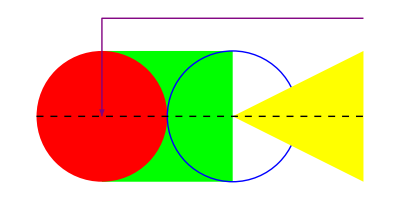
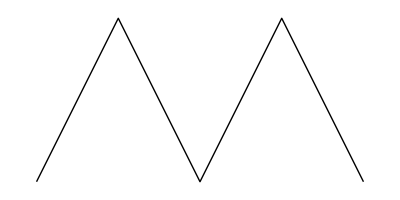
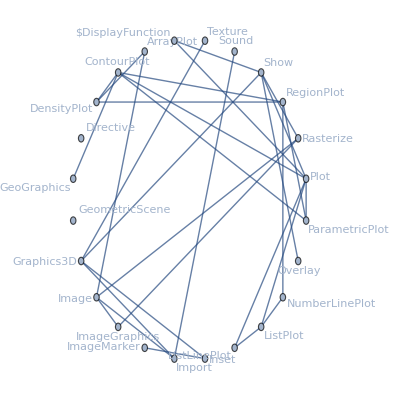
attributes | {Protected,ReadProtected}
character count | 8
common option values | {Epilog→{},Method→{{"AxesInFront"->False},{"FrameInFront"->False},{"GridLinesInFront"->True},{"TransparentPolygonMesh"->True}}}
date introduced | Day: Thu 23 Jun 1988
date last modified | Day: Wed 9 Jul 2014
dates modified | {Day: Tue 3 Sep 1996,Day: Tue 1 May 2007,Day: Tue 18 Nov 2008,Day: Mon 15 Nov 2010,Day: Wed 9 Jul 2014}
documentation basic examples | {{Use lines, polygons, circles, etc. to build up a graphics image:,Graphics[{Thick,Green,Rectangle[{0,-1},{2,1}],Red,Disk[],Blue,Circle[{2,0}],Yellow,Polygon[{{2,0},{4,1},{4,-1}}],Purple,Arrowheads[Large],Arrow[{{4,3/2},{0,3/2},{0,0}}],Black,Dashed,Line[{{-1,0},{4,0}}]}],-Graphics-}}
documentation example counts | {BasicExamples→2,Scope→13,GeneralizationsExtensions→0,Options→68,Applications→1,PropertiesRelations→5,PossibleIssues→0,InteractiveExamples→0,NeatExamples→2}
documentation example inputs | {BasicExamples→{{Graphics[{Thick,Green,Rectangle[{0,-1},{2,1}],Red,Disk[],Blue,Circle[{2,0}],Yellow,Polygon[{{2,0},{4,1},{4,-1}}],Purple,Arrowheads[Large],Arrow[{{4,3/2},{0,3/2},{0,0}}],Black,Dashed,Line[{{-1,0},{4,0}}]}]},{Plot[Evaluate[Table[BesselJ[n,x],{n,4}]],{x,0,10},Filling→Axis],GraphPlot[Table[i→Mod[i^2,102],{i,0,102}]],ReliefPlot[Table[i+Sin[i^2+j^2],{i,-4,4,.03},{j,-4,4,.03}],ColorFunction→SunsetColors]}},Scope→{{Graphics[{Red,Disk[],Green,Rectangle[{0,0},{2,2}],Blue,Disk[{2,2}]}]},{Graphics[Polygon[{{0,0},{1,1},{0,1},{1,0}}]]},{v=Table[15{Cos[t],Sin[t]},{t,0,4Pi,4Pi/5}];,Graphics[GraphicsComplex[v,{Point[{1,2,3,4,5,6}],Green,Line[{1,2,3,4,5,6}]}]]},{Graphics[{Circle[],Inset[x^2+y^2==1,{0,0}]}]},{{Graphics[{Red,Disk[]}],Graphics[{Green,Disk[],Yellow,Opacity[.7],Disk[{0,1}]}],
Graphics[{Hue[2/3,1/2,1],Rectangle[]}]}},{{Graphics[{Blue,Arrow[{{0,0},{2,1}}]}],Graphics[{Thick,Blue,Line[{{0,0},{2,1}}]}],Graphics[{Dashed,Red,Arrow[{{0,0},{2,1}}]}],Graphics[{Thick,Dashed,Red,Line[{{0,0},{2,1}}]}]},{Graphics[{Pink,Rectangle[]}],Graphics[{EdgeForm[Thick],Pink,Rectangle[]}],Graphics[{EdgeForm[Dashed],Pink,Rectangle[]}],Graphics[{EdgeForm[Directive[Thick,Dashed,Blue]],Pink,Rectangle[]}]}},{{Graphics[{Dashed,Red,Arrowheads[{-.1,.1}],Arrow[{{0,0},{2,1}}]}],Graphics[{Blue,PointSize[Large],Point[{{0,0},{1,1/2},{2,1}}]}]}},{Graphics[{Style[Disk[],Pink],Style[Rectangle[{2,-1},{4,1}],Blue]}]},{Graphics[{Pink,Disk[],{Blue,Disk[{1,0}]},Disk[{2,0}]}]},{Graphics[Rectangle[{0,4},{10,6}],Frame→True,PlotRange→{{0,10},{0,10}}]},{Graphics[Rectangle[Scaled[{0,.4}],Scaled[{1,.6}]],Frame→True,PlotRange→{{0,10},{0,10}}]},{Graphics[Rectangle[ImageScaled[{0,.4}],ImageScaled[{1,.6}]],Frame→True,PlotRange→{{0,10},{0,10}}]},{Graphics[Rectangle[Offset[{10,20},{0,0}],Offset[{-10,-20},{1,1}]],Frame→True]}},GeneralizationsExtensions→{},Options→{{Table[Graphics[{Inset[Graphics[Circle[],ImageSize→30,AlignmentPoint→{a,0}],Center]},ImageSize→70,Axes→True,Ticks→None],{a,{-1,0,1}}],Table[Graphics[{Inset[Graphics[Circle[],ImageSize→30,AlignmentPoint→{0,a}],Center]},ImageSize→70,Axes→True,Ticks→None],{a,{-1,0,1}}]},{Table[Graphics[Circle[],AspectRatio→1/k],{k,1,3}]},{Graphics[Circle[],Axes→True]},{Graphics[Circle[],Axes→{False,True}]},{Graphics[Circle[],Axes→True,AxesLabel→y]},{Graphics[Circle[],Axes→True,AxesLabel→{x,y}]},{Graphics[Circle[],Axes→True,AxesOrigin→Automatic]},{Graphics[Circle[],Axes→True,AxesOrigin→{0,-1}]},{Graphics[Circle[],Axes→True,AxesStyle→Directive[Orange,12]],Graphics[Circle[],Axes→True,AxesStyle→{Directive[Dashed,Red],Blue}]},{Graphics[Circle[],Background→LightBlue]},{{x,Graphics[Circle[],ImageSize→50,BaselinePosition→Center],y}},{Table[{x,Graphics[Circle[],BaselinePosition→Scaled[b],ImageSize→50]},{b,{0,0.5,1}}]},{{x,Graphics[Circle[],Axes→True,BaselinePosition→Axis],y},{x,Graphics[Circle[{0,1}],Axes→True,BaselinePosition→Axis],y}},{Graphics[{Circle[{0,0},1],Disk[{3,0},1]},BaseStyle→Blue]},{Graphics[{Circle[{0,0},1],Disk[{3,0},1]},BaseStyle→{Green,Thick,EdgeForm[Dashed]}]},{Graphics[{Pink,Disk[],Rectangle[{2,-1},{4,1}]},ContentSelectable→True]},{Graphics[{Pink,Disk[],Rectangle[{2,-1},{4,1}]},ContentSelectable→False]},{Graphics[{Pink,Disk[],Rectangle[{2,-1},{4,1}]},ContentSelectable→Automatic]},{Graphics[{Pink,Disk[]},Axes→True,Epilog→{Blue,Disk[{0,0},.4]}]},{Graphics[{Circle[],Text[Style[x^2+y^2==1,20]]}]},{Graphics[{Circle[],Text[Style[x^2+y^2==1,20]]},FormatType→StandardForm]},{Graphics[Circle[],Axes→True,AxesLabel→{Cos[θ],Sin[θ]},FormatType→StandardForm]},{Graphics[Circle[],Frame→True]},{Graphics[Circle[],Frame→{{True,True},{False,False}}]},{Graphics[Circle[],Frame→True,FrameLabel→{x,y}],Graphics[Circle[],Frame→True,FrameLabel→{{a,b},{c,d}}]},{Graphics[Circle[],Frame→True,FrameStyle→Directive[Thick,Gray]]},{Graphics[Circle[],Frame→True,FrameStyle→{{Thick,Directive[Thick,Dashed]},{Blue,Red}}]},{Graphics[Circle[],Frame→True,FrameTicks->None],Graphics[Circle[],Frame→True,FrameTicks→Automatic]},{Graphics[Circle[],Frame→True,FrameTicks→{{None,Automatic},{Automatic,None}}]},{Graphics[{},Frame→True,FrameTicksStyle→Directive[Orange,12]]},{Graphics[{},Frame→True,FrameTicks→All,FrameTicksStyle→{{Black,Blue},{Red,Green}}]},{Graphics[Circle[],GridLines→Automatic]},{Graphics[Circle[],Axes→True,GridLines→{{-1,1},{-1,1}}]},{Graphics[Circle[],Axes→True,GridLines→{{{-1,Orange},{-.5,Dotted},{.5,Dotted},{1,Orange}},{-1,{-.5,Dotted},{.5,Dotted},1}}]},{Graphics[Circle[],Axes→True,GridLines→Automatic,GridLinesStyle→Directive[Red,Dotted]]},{Framed[Graphics[Disk[]]]},{Framed[Graphics[Disk[],ImageMargins→20]]},{Framed[Graphics[Disk[],ImageMargins→{{5,10},{20,30}}]]},{Graphics[{Thickness[.3],Pink,Circle[]},ImagePadding→None,Frame→True,FrameLabel→{x,y}]},{Framed[Graphics[{Thickness[.3],Pink,Circle[]},ImagePadding→All,Frame→True,FrameLabel→{x,y}],FrameMargins→0]},{Framed[Graphics[{Thickness[.3],Pink,Circle[]},ImagePadding→40,Frame→True]]},{Framed[Graphics[{Thickness[.2],Pink,Circle[]},ImagePadding→{{40,10},{20,5}},Frame→True]]},{Table[Graphics[Circle[],ImageSize→s],{s,{Tiny,Small}}]},{{Graphics[Circle[],ImageSize→100],Graphics[Circle[{0,0},{1,2}],ImageSize→100]}},{{Graphics[Circle[],ImageSize→{100,100}],Graphics[Circle[{0,0},{1,2}],ImageSize→{100,100}]}},{Graphics[Circle[],Axes→True,AxesLabel→{x,y},LabelStyle→Orange]},{Graphics[{Red,Table[Disk[{i,i}],{i,-1,1}]},Axes→True,Method→{AxesInFront→False}],Graphics[{Red,Polygon[{{0.5,0},{.5,1},{-.5,1}}]},Frame→True,PlotRange→{{0,1},{0,1}}],Show[%, Method→{FrameInFront→False}],Graphics[{Green,PointSize[.6],Point[{0,0}]},GridLines→Automatic,Method→{GridLinesInFront→True}],Graphics[{Blue,Opacity[0.2],EdgeForm[None],
Polygon[{{{0,0},{0,1},{1,0}},{{1,1},{0,1},{1,0}}}]}],Show[%,Method→{TransparentPolygonMesh→True}]},{Graphics[Circle[],PlotLabel→x^2+y^2==1]},{Graphics[Circle[],PlotLabel→Style[Framed[x^2+y^2==1],16,Red,Background→Yellow]]},{Graphics[{Pink,Disk[{0,0},5]},Frame→True,PlotRange→All]},{Graphics[{Pink,Disk[]},PlotRange→{{-1,1},{0,1}},Frame→True],Graphics[{Pink,Disk[]},PlotRange→{{-1,1},{0,1}},PlotRangeClipping→True,Frame→True]},{Graphics[{Pink,Disk[{0,0},5]},Frame→True,PlotRange→4]},{Graphics[{Pink,Disk[{0,0},5]},Frame→True,PlotRange→4,PlotRangeClipping→False]},{Graphics[{Pink,Disk[{0,0},5]},Frame→True,PlotRange→4,PlotRangeClipping→True]},{Graphics[{Pink,Rectangle[]},PlotRangePadding→1,Frame→True]},{Graphics[{Pink,Rectangle[]},PlotRangePadding→Scaled[0.1],Frame→True]},{Graphics[{Pink,Rectangle[]},PlotRangePadding→{{0.5,1},{0.3,0.3}},Frame→True]},{Graphics[{Pink,Disk[]},Frame→True,FrameTicks→False,Background→LightBlue]},{Graphics[{Pink,Disk[]},Frame→True,FrameTicks→False,PlotRegion→{{0.25,0.75},{0.25,0.75}},Background→LightBlue]},{Graphics[{Pink,Disk[]},Frame→True,FrameTicks→False,ImagePadding→30,Background→LightBlue]},{bg=Graphics[Polygon[{{0,0},{1,0},{1,1},{0,1}},VertexColors→{Orange,Orange,White,White}],AspectRatio→Full];,Graphics[Circle[],Prolog→Inset[bg,Scaled[{0,0}],Scaled[{0,0}]]],Plot[Sin[x],{x,0,10},Prolog→Inset[bg,Scaled[{0,0}],Scaled[{0,0}],Scaled[{1,1}]]]},{Graphics[Circle[],Frame→True,FrameLabel→{None,y axis},RotateLabel→True]},{Graphics[Circle[],Frame→True,FrameLabel→{None,y axis},RotateLabel→False]},{Graphics[Circle[],Axes→True,Ticks→None]},{Graphics[Circle[],Axes→True,Ticks→Automatic]},{Graphics[Circle[{0,0},3],Ticks→{{1,2,3},{1,3}},Axes→True]},{Graphics[Circle[],Axes→True,TicksStyle→Directive[Red,Bold]]},{Graphics[Circle[],Axes→True,TicksStyle→{Directive[Red,Bold],Directive[Blue,12]}]}},Applications→{{pts=Table[{Cos[2n π/9],Sin[2 n π/9]},{n,0,8}];,Graphics[{Opacity[0.7],Red,Line[Tuples[pts,2]],Blue,PointSize[0.05],Point[pts]}]}},PropertiesRelations→{{Graphics[Disk[]],InputForm[%]},{makeDashed[ g_Graphics ]:=g/.l_Line:>{Dashed,l},makeDashed[-Graphics-]},{ParametricPlot[{(v+u) Cos[u],(v+u) Sin[u]},{u,0,4Pi},{v,0,5},Mesh→False],ContourPlot[y+Sin[x^2+3y],{x,-3,3},{y,-3,3},ColorFunction→Rainbow]},{CountryData[World,Shape],GraphData[DoubleStarSnark]},{First@Import[ExampleData/mathematica.pdf],Import[ExampleData/coneflower.jpg, Graphics]}},PossibleIssues→{},InteractiveExamples→{},NeatExamples→{{Dynamic@Module[{hour,min,sec,ht,mt,st},Clock[];{hour,min,sec}=Take[DateList[],-3];ht=Pi/2-2Pi hour/12-2Pi min/720;mt=Pi/2-2Pi min/60;st=Pi/2-2Pi Floor[sec]/60;Graphics[{Arrowheads[0.1],Arrow[{{0,0},0.6{Cos[ht],Sin[ht]}}],Arrow[{{0,0},0.85{Cos[mt],Sin[mt]}}],Line[{{0,0},0.85{Cos[st],Sin[st]}}],PointSize[Medium],Table[Point[0.9{Cos[i],Sin[i]}],{i,0,2Pi,Pi/6}],Point[{0,0}],Circle[]}]]},{Graphics[Table[{Hue[t/20],Circle[{Cos[2Pi t/20],Sin[2Pi t/20]}]},{t,20}]]}}}
documentation example text | {BasicExamples→{{Use lines, polygons, circles, etc. to build up a graphics image:},{Use plot functions to automatically create Graphics from different types of data: }},Scope→{{Graphics primitives are drawn in the order in which they are given in Graphics:},{Polygons can fold over themselves:},{Vertices can be shared by using GraphicsComplex:},{Inset an expression in a graphic:},{Directives can specify color and opacity of faces:},{Colors, thickness, and dashing directives affect lines, arrows, and edges:},{Some primitives have special directives to specify various properties:},{Directives can be applied to individual objects using Style:},{Graphics directives remain in effect only until the end of the list that contains them:},{Use an ordinary coordinate system:},{Specify coordinates by fractions of the plot range:},{Specify coordinates by fractions of the whole image:},{Offset coordinates by printer's points:}},GeneralizationsExtensions→{},Options→{{Specify the coordinates within Inset to be aligned with the center of the enclosing graphic:},{Use numerical values for AspectRatio:},{Draw all the axes:},{Draw the y axis but not the x axis:},{Place a label for the y axis:},{Specify a label for each axis:},{Determine where the axes cross automatically:},{Specify the axes' origin explicitly:},{Specify the overall axes style, including the ticks and the tick labels:,Specify the style of each axis:},{Specify a background color:},{Align the center of a graphic with the baseline of the text:},{Specify the baseline of a graphic as a fraction of the height by using Scaled:},{Use the axis of a graphic as the baseline:},{Set the starting style:},{Set multiple starting styles:},{Allow the individual graphics objects to be selectable by a single click:},{No individual object is selectable; the whole graphic appears as one object:},{The first click selects the whole graphic, and subsequent ones select individual objects:},{Draw a disk above the graphic, including the axes:},{By default, expressions are displayed using TraditionalForm in graphics:},{Display expressions using StandardForm:},{Labels are also affected by FormatType setting:},{Draw a frame around the whole graphic:},{Draw a frame on the left and the right edges:},{Specify frame labels for the bottom and the left edges:,Specify labels for each edge:},{Specify the overall frame style:},{Specify the style of each frame edge:},{Put a frame, but no ticks:,Tick mark labels on the bottom and the left frame edges:},{Frame ticks on the bottom and the right edges:},{Specify frame tick and frame tick label style:},{Specify frame tick style for each edge:},{Put grids across a 2D graphic:},{Draw grid lines at specific positions:},{Specify the style of each grid:},{Specify the overall grid style:},{Allow no margins outside of ImageSize:},{Have 20-point margins on all sides:},{Leave different margins on each side:},{Leave no padding outside of the plot range:},{Leave enough padding for all objects and labels that are present:},{Specify the same padding for all sides in printer's points:},{Specify different padding on each side:},{Use predefined symbolic sizes:},{Use an explicit image width:},{Use an explicit image width and height:},{Specify the overall style of all the label-like elements:},{Force axes to be behind drawing primitives:,By default, frames draw in front of graphics primitives:,Force the frame to draw behind graphics primitives:,Force grid lines to be rendered in front of graphics primitives:,By default, polygon meshes double-paint their edges for efficiency reasons:,The behavior can be turned off using the TransparentPolygonMesh method option:},{Display a label on the top of the graphic in TraditionalForm:},{Use Style and other typesetting functions to modify how the label appears:},{Display all objects:},{Explicitly choose x and y ranges:,Force clipping at the PlotRange: },{PlotRange->s is equivalent to PlotRange->{{-s,s},{-s,s}}:},{Allow graphics objects to spread beyond PlotRange:},{Clip all graphics objects at PlotRange:},{Include 1 coordinate unit of padding on all sides:},{Include padding using Scaled coordinates: },{Specify different padding on each side:},{The contents of a graphic use the whole region:},{Limit the contents of the graphic to the middle half of the region in each direction:},{ImagePadding can also be used to add padding around a graphic:},{Define a simple graphic to use as a background:,Use it in multiple graphics:},{Specify that vertical frame labels should be rotated:},{Specify that vertical frame labels should not be rotated:},{Draw the axes but no tick marks:},{Place tick marks automatically:},{Draw tick marks at the specific positions:},{Specify the styles of the ticks and tick labels:},{Specify the styles of x and y axis ticks separately:}},Applications→{{Draw a complete graph with 9 vertices:}},PropertiesRelations→{{The StandardForm of Graphics is its rendered form:,The InputForm is the textual expression form:},{Graphics can be used as input to functions: },{Two-dimensional plot functions return Graphics:},{Several integrated data sources return Graphics:},{Many Import and Export formats support Graphics:}},PossibleIssues→{},InteractiveExamples→{},NeatExamples→{{Display an analog clock with current system time:},{Digital dahlias:}}}
entity classes | {}
eponymous people | {}
equal-precedence symbols | Missing[NotApplicable]
external links | {Fast Introduction for Programmers: Graphics→http://www.wolfram.com/language/fast-introduction-for-programmers/graphics/}
frequencies of usage | {All→0.000574249,StackExchange→0.00205678,TypicalProductionCode→0.00141163,WolframAlphaCodebase→0.000162146,WolframDemonstrations→0.00266587,WolframDocumentation→0.00331944}
full version introduced | 1
full version last modified | 10
full versions modified | {3,6,7,8,10}
functionality areas | {BasicSymbols}
symbol background | Missing[NotAvailable]
keyboard shortcuts | Missing[NotAvailable]
link trails | {{guide/WolframRoot,guide/SymbolicGraphicsLanguage,ref/Graphics},{guide/WolframRoot,guide/MapsAndCartography,guide/SymbolicGraphicsLanguage,ref/Graphics},{guide/WolframRoot,guide/GeographicData,guide/MapsAndCartography,guide/SymbolicGraphicsLanguage,ref/Graphics},{guide/WolframRoot,guide/GeometricComputation,guide/Polygons,guide/SymbolicGraphicsLanguage,ref/Graphics},{guide/WolframRoot,guide/GeometricComputation,guide/Polyhedra,guide/SymbolicGraphicsLanguage,ref/Graphics},{guide/WolframRoot,guide/LocationsPathsAndRouting,guide/MapsAndCartography,guide/SymbolicGraphicsLanguage,ref/Graphics},{guide/WolframRoot,guide/3DPrinting,guide/GeometricComputation,guide/Polygons,guide/SymbolicGraphicsLanguage,ref/Graphics},{guide/WolframRoot,guide/3DPrinting,guide/GeometricComputation,guide/Polyhedra,guide/SymbolicGraphicsLanguage,ref/Graphics},{guide/WolframRoot,guide/Calculus,guide/GeometricComputation,guide/Polygons,guide/SymbolicGraphicsLanguage,ref/Graphics},{guide/WolframRoot,guide/Calculus,guide/GeometricComputation,guide/Polyhedra,guide/SymbolicGraphicsLanguage,ref/Graphics},{guide/WolframRoot,guide/EarthSciencesDataAndComputation,guide/GeographicData,guide/MapsAndCartography,guide/SymbolicGraphicsLanguage,ref/Graphics},{guide/WolframRoot,guide/Geodesy,guide/LocationsPathsAndRouting,guide/MapsAndCartography,guide/SymbolicGraphicsLanguage,ref/Graphics},{guide/WolframRoot,guide/PlaneGeometry,guide/GeometricComputation,guide/Polygons,guide/SymbolicGraphicsLanguage,ref/Graphics},{guide/WolframRoot,guide/PlaneGeometry,guide/GeometricComputation,guide/Polyhedra,guide/SymbolicGraphicsLanguage,ref/Graphics},{guide/WolframRoot,guide/SolidGeometry,guide/GeometricComputation,guide/Polygons,guide/SymbolicGraphicsLanguage,ref/Graphics},{guide/WolframRoot,guide/SolidGeometry,guide/GeometricComputation,guide/Polyhedra,guide/SymbolicGraphicsLanguage,ref/Graphics},{guide/WolframRoot,guide/DateAndTime,guide/Geodesy,guide/LocationsPathsAndRouting,guide/MapsAndCartography,guide/SymbolicGraphicsLanguage,ref/Graphics},{guide/WolframRoot,guide/DiscreteCalculus,guide/Calculus,guide/GeometricComputation,guide/Polygons,guide/SymbolicGraphicsLanguage,ref/Graphics},{guide/WolframRoot,guide/DiscreteCalculus,guide/Calculus,guide/GeometricComputation,guide/Polyhedra,guide/SymbolicGraphicsLanguage,ref/Graphics},{guide/WolframRoot,guide/EarthSciencesDataAndComputation,guide/Geodesy,guide/LocationsPathsAndRouting,guide/MapsAndCartography,guide/SymbolicGraphicsLanguage,ref/Graphics},{guide/WolframRoot,guide/GeometricSolvers,guide/PDEModelingAndAnalysis,guide/GeometricComputation,guide/Polygons,guide/SymbolicGraphicsLanguage,ref/Graphics},{guide/WolframRoot,guide/GeometricSolvers,guide/PDEModelingAndAnalysis,guide/GeometricComputation,guide/Polyhedra,guide/SymbolicGraphicsLanguage,ref/Graphics},{guide/WolframRoot,guide/PlaneGeometry,guide/SolidGeometry,guide/GeometricComputation,guide/Polygons,guide/SymbolicGraphicsLanguage,ref/Graphics},{guide/WolframRoot,guide/PlaneGeometry,guide/SolidGeometry,guide/GeometricComputation,guide/Polyhedra,guide/SymbolicGraphicsLanguage,ref/Graphics},{guide/WolframRoot,guide/ScientificModels,guide/Calculus,guide/GeometricComputation,guide/Polygons,guide/SymbolicGraphicsLanguage,ref/Graphics},{guide/WolframRoot,guide/ScientificModels,guide/Calculus,guide/GeometricComputation,guide/Polyhedra,guide/SymbolicGraphicsLanguage,ref/Graphics},{guide/WolframRoot,guide/SolidGeometry,guide/PlaneGeometry,guide/GeometricComputation,guide/Polygons,guide/SymbolicGraphicsLanguage,ref/Graphics},{guide/WolframRoot,guide/SolidGeometry,guide/PlaneGeometry,guide/GeometricComputation,guide/Polyhedra,guide/SymbolicGraphicsLanguage,ref/Graphics},{guide/WolframRoot,guide/CloudFunctionsAndDeployment,guide/CloudExecutionMetadata,guide/Geodesy,guide/LocationsPathsAndRouting,guide/MapsAndCartography,guide/SymbolicGraphicsLanguage,ref/Graphics},{guide/WolframRoot,guide/CreatingAnInstantAPI,guide/CloudExecutionMetadata,guide/Geodesy,guide/LocationsPathsAndRouting,guide/MapsAndCartography,guide/SymbolicGraphicsLanguage,ref/Graphics},{guide/WolframRoot,guide/CreatingFormsAndApps,guide/CloudExecutionMetadata,guide/Geodesy,guide/LocationsPathsAndRouting,guide/MapsAndCartography,guide/SymbolicGraphicsLanguage,ref/Graphics},{guide/WolframRoot,guide/DiscreteMathematics,guide/DiscreteCalculus,guide/Calculus,guide/GeometricComputation,guide/Polygons,guide/SymbolicGraphicsLanguage,ref/Graphics},{guide/WolframRoot,guide/DiscreteMathematics,guide/DiscreteCalculus,guide/Calculus,guide/GeometricComputation,guide/Polyhedra,guide/SymbolicGraphicsLanguage,ref/Graphics},{guide/WolframRoot,guide/Finance,guide/DateAndTime,guide/Geodesy,guide/LocationsPathsAndRouting,guide/MapsAndCartography,guide/SymbolicGraphicsLanguage,ref/Graphics},{guide/WolframRoot,guide/GeographicData,guide/EarthSciencesDataAndComputation,guide/Geodesy,guide/LocationsPathsAndRouting,guide/MapsAndCartography,guide/SymbolicGraphicsLanguage,ref/Graphics},{guide/WolframRoot,guide/InternetAndWebRelatedData,guide/CloudExecutionMetadata,guide/Geodesy,guide/LocationsPathsAndRouting,guide/MapsAndCartography,guide/SymbolicGraphicsLanguage,ref/Graphics},{guide/WolframRoot,guide/MeshRegions,guide/GeometricSolvers,guide/PDEModelingAndAnalysis,guide/GeometricComputation,guide/Polygons,guide/SymbolicGraphicsLanguage,ref/Graphics},{guide/WolframRoot,guide/MeshRegions,guide/GeometricSolvers,guide/PDEModelingAndAnalysis,guide/GeometricComputation,guide/Polyhedra,guide/SymbolicGraphicsLanguage,ref/Graphics},{guide/WolframRoot,guide/PeopleAndHistory,guide/DateAndTime,guide/Geodesy,guide/LocationsPathsAndRouting,guide/MapsAndCartography,guide/SymbolicGraphicsLanguage,ref/Graphics},{guide/WolframRoot,guide/PhysicsAndChemistryDataAndComputation,guide/ScientificModels,guide/Calculus,guide/GeometricComputation,guide/Polygons,guide/SymbolicGraphicsLanguage,ref/Graphics},{guide/WolframRoot,guide/PhysicsAndChemistryDataAndComputation,guide/ScientificModels,guide/Calculus,guide/GeometricComputation,guide/Polyhedra,guide/SymbolicGraphicsLanguage,ref/Graphics},{guide/WolframRoot,guide/PlaneGeometry,guide/GeometricSolvers,guide/PDEModelingAndAnalysis,guide/GeometricComputation,guide/Polygons,guide/SymbolicGraphicsLanguage,ref/Graphics},{guide/WolframRoot,guide/PlaneGeometry,guide/GeometricSolvers,guide/PDEModelingAndAnalysis,guide/GeometricComputation,guide/Polyhedra,guide/SymbolicGraphicsLanguage,ref/Graphics},{guide/WolframRoot,guide/ScientificDataAnalysis,guide/ScientificModels,guide/Calculus,guide/GeometricComputation,guide/Polygons,guide/SymbolicGraphicsLanguage,ref/Graphics},{guide/WolframRoot,guide/ScientificDataAnalysis,guide/ScientificModels,guide/Calculus,guide/GeometricComputation,guide/Polyhedra,guide/SymbolicGraphicsLanguage,ref/Graphics},{guide/WolframRoot,guide/SolidGeometry,guide/GeometricSolvers,guide/PDEModelingAndAnalysis,guide/GeometricComputation,guide/Polygons,guide/SymbolicGraphicsLanguage,ref/Graphics},{guide/WolframRoot,guide/SolidGeometry,guide/GeometricSolvers,guide/PDEModelingAndAnalysis,guide/GeometricComputation,guide/Polyhedra,guide/SymbolicGraphicsLanguage,ref/Graphics},{guide/WolframRoot,guide/TimeSeries,guide/DateAndTime,guide/Geodesy,guide/LocationsPathsAndRouting,guide/MapsAndCartography,guide/SymbolicGraphicsLanguage,ref/Graphics}}
memberships | {}
name | Graphics
option names | {AlignmentPoint,AspectRatio,Axes,AxesLabel,AxesOrigin,AxesStyle,Background,BaselinePosition,BaseStyle,ColorOutput,ContentSelectable,CoordinatesToolOptions,DisplayFunction,Epilog,FormatType,Frame,FrameLabel,FrameStyle,FrameTicks,FrameTicksStyle,GridLines,GridLinesStyle,ImageMargins,ImagePadding,ImageSize,ImageSizeRaw,LabelStyle,Method,PlotLabel,PlotRange,PlotRangeClipping,PlotRangePadding,PlotRegion,PreserveImageOptions,Prolog,RotateLabel,Ticks,TicksStyle}
options | {AlignmentPoint→Center,AspectRatio→Automatic,Axes→False,AxesLabel→None,AxesOrigin→Automatic,AxesStyle→{},Background→None,BaselinePosition→Automatic,BaseStyle→{},ColorOutput→Automatic,ContentSelectable→Automatic,CoordinatesToolOptions→Automatic,DisplayFunction:>$DisplayFunction,Epilog→{},FormatType:>TraditionalForm,Frame→False,FrameLabel→None,FrameStyle→{},FrameTicks→Automatic,FrameTicksStyle→{},GridLines→None,GridLinesStyle→{},ImageMargins→0.,ImagePadding→All,ImageSize→Automatic,ImageSizeRaw→Automatic,LabelStyle→{},Method→Automatic,PlotLabel→None,PlotRange→All,PlotRangeClipping→False,PlotRangePadding→Automatic,PlotRegion→Automatic,PreserveImageOptions→Automatic,Prolog→{},RotateLabel→True,Ticks→Automatic,TicksStyle→{}}
plaintext usage | Graphics[primitives, options] represents a two-dimensional graphical image.
precedence ranks | Missing[NotApplicable]
ranks of usage | {All→72,StackExchange→47,TypicalProductionCode→66,WolframAlphaCodebase→111,WolframDemonstrations→38,WolframDocumentation→24}
related entities | Missing[NotAvailable]
related guide pages | {Plane Geometrypaclet:guide/PlaneGeometry,Symbolic Graphics Languagepaclet:guide/SymbolicGraphicsLanguage,Polygonspaclet:guide/Polygons,Polygonspaclet:guide/PolygonsNew,Polygons & Polyhedrapaclet:guide/PolygonsAndPolyhedra,Popular Functionspaclet:guide/PopularFunctions,Graphics & Visualizationpaclet:guide/GraphicsAndVisualization,WDF (Wolfram Data Framework)paclet:guide/WDFWolframDataFramework}
related symbols | {Plot,ListPlot,ListLinePlot,ParametricPlot,DensityPlot,ArrayPlot,RegionPlot,ContourPlot,Show,Graphics3D,Image,Import,GeometricScene,Sound}
relationship community graph | -Graphics-
relationship graph | -Graphics-
short notations | Missing[NotApplicable]
subject classifications | Missing[NotAvailable]
symbols linking to | {Directive,GeoGraphics,GeometricScene,Graphics3D,Image,ImageGraphics,ImageMarker,Inset,ListLinePlot,ListPlot,NumberLinePlot,Overlay,ParametricPlot,Plot,Rasterize,Sound,Texture,$DisplayFunction}
symbols using as attribute | {}
symbols using as option | {}
text strings | {Graphics[primitives,options] represents a two-dimensional graphical image.,Graphics is displayed in StandardForm as a graphical image. In InputForm, it is displayed as an explicit list of primitives.,The following graphics primitives can be used:139436543,The following graphics directives can be used:362437821,The following wrappers can be used at any level:,The following options can be given:,Nested lists of graphics constructs can be given. Directive specifications such as GrayLevel remain in effect only until the end of the list that contains them.415812662,Style[obj,opts] can be used to apply the options or directives opts to obj.59755747,The following Method options can be given:,The settings for BaseStyle are appended to the default style typically given by the "Graphics" style in the current stylesheet. The settings for AxesStyle, LabelStyle, etc. are appended to the default styles given for "GraphicsAxes", "GraphicsLabel", etc.,Graphics[] gives an empty graphic with the default image size.,Use lines, polygons, circles, etc. to build up a graphics image:,Use plot functions to automatically create Graphics from different types of data:,Graphics primitives are drawn in the order in which they are given in Graphics:,Polygons can fold over themselves:,Vertices can be shared by using GraphicsComplex:,Inset an expression in a graphic:,Directives can specify color and opacity of faces:,Colors, thickness, and dashing directives affect lines, arrows, and edges:,Some primitives have special directives to specify various properties:,Directives can be applied to individual objects using Style:,Graphics directives remain in effect only until the end of the list that contains them:,Use an ordinary coordinate system:,Specify coordinates by fractions of the plot range:,Specify coordinates by fractions of the whole image:,Offset coordinates by printer's points:,Specify the coordinates within Inset to be aligned with the center of the enclosing graphic:,Use numerical values for AspectRatio:,Draw all the axes:,Draw the y axis but not the x axis:,Place a label for the y axis:,Specify a label for each axis:,Determine where the axes cross automatically:,Specify the axes' origin explicitly:,Specify the overall axes style, including the ticks and the tick labels:,Specify the style of each axis:,Specify a background color:,Align the center of a graphic with the baseline of the text:,Specify the baseline of a graphic as a fraction of the height by using Scaled:,Use the axis of a graphic as the baseline:,Set the starting style:,Set multiple starting styles:,Allow the individual graphics objects to be selectable by a single click:,No individual object is selectable; the whole graphic appears as one object:,The first click selects the whole graphic, and subsequent ones select individual objects:,Draw a disk above the graphic, including the axes:,By default, expressions are displayed using TraditionalForm in graphics:,Display expressions using StandardForm:,Labels are also affected by FormatType setting:,Draw a frame around the whole graphic:,Draw a frame on the left and the right edges:,Specify frame labels for the bottom and the left edges:,Specify labels for each edge:,Specify the overall frame style:,Specify the style of each frame edge:,Put a frame, but no ticks:,Tick mark labels on the bottom and the left frame edges:,Frame ticks on the bottom and the right edges:,Specify frame tick and frame tick label style:,Specify frame tick style for each edge:,Put grids across a 2D graphic:,Draw grid lines at specific positions:,Specify the style of each grid:,Specify the overall grid style:,Allow no margins outside of ImageSize:,Have 20-point margins on all sides:,Leave different margins on each side:,Leave no padding outside of the plot range:,Leave enough padding for all objects and labels that are present:,Specify the same padding for all sides in printer's points:,Specify different padding on each side:,Use predefined symbolic sizes:,Use an explicit image width:,Use an explicit image width and height:,Specify the overall style of all the label-like elements:,Force axes to be behind drawing primitives:,By default, frames draw in front of graphics primitives:,Force the frame to draw behind graphics primitives:,Force grid lines to be rendered in front of graphics primitives:,By default, polygon meshes double-paint their edges for efficiency reasons:,The behavior can be turned off using the "TransparentPolygonMesh" method option:,Display a label on the top of the graphic in TraditionalForm:,Use Style and other typesetting functions to modify how the label appears:,Display all objects:,Explicitly choose x and y ranges:,Force clipping at the PlotRange:,PlotRange->s is equivalent to PlotRange->{{-s,s},{-s,s}}:,Allow graphics objects to spread beyond PlotRange:,Clip all graphics objects at PlotRange:,Include 1 coordinate unit of padding on all sides:,Include padding using Scaled coordinates:,Specify different padding on each side:,The contents of a graphic use the whole region:,Limit the contents of the graphic to the middle half of the region in each direction:,ImagePadding can also be used to add padding around a graphic:,Define a simple graphic to use as a background:,Use it in multiple graphics:,Specify that vertical frame labels should be rotated:,Specify that vertical frame labels should not be rotated:,Draw the axes but no tick marks:,Place tick marks automatically:,Draw tick marks at the specific positions:,Specify the styles of the ticks and tick labels:,Specify the styles of x and y axis ticks separately:,Draw a complete graph with 9 vertices:,The StandardForm of Graphics is its rendered form:,The InputForm is the textual expression form:,Graphics can be used as input to functions:,Two-dimensional plot functions return Graphics:,Several integrated data sources return Graphics:,Many Import and Export formats support Graphics:,Display an analog clock with current system time:,Digital dahlias:}
timeline | -Graphics-
timeline events | Interval[{Day: Thu 23 Jun 1988,Day: Wed 9 Jul 2014}]Graphics
translations | {Simplified Chinese→图形,Traditional Chinese→圖形,French→graphique,German→Graphik,Modern Greek→γραφικά,Japanese→グラフィックス,Korean→그래픽,Lithuanian→grafika,Polish→grafika,Portuguese→representação gráfica,Russian→графика,Spanish→gráfico,Ukrainian→графіка,Vietnamese→đồ họa}
typeset usage | Graphics[primitives,options] represents a two-dimensional graphical image. 
URL | http://reference.wolfram.com/language/ref/Graphics.html
version introduced | 1
version last modified | 10
versions modified | {3,6,7,8,10}
Wolfram documentation link | Graphicspaclet:ref/Graphics

```mathematica
Grid[MapThread[{#1,#2}&,{wlEntityProperties,graphicsWLProperties}],Frame->All]
```

```mathematica
simplePlot=Plot[2 x, {x,-2,2}];
```

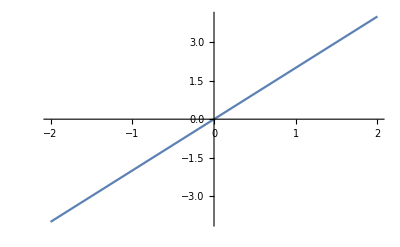

```mathematica
simplePlot
```

```mathematica
simplePlotFullForm = FullForm[simplePlot];
```

```mathematica
simplePlotInputForm = InputForm[simplePlot];
```

```mathematica
simplePlotFullForm
```

Graphics[List[List[List[List[],List[],Annotation[List[Directive[Opacity[1.],RGBColor[0.368417,0.506779,0.709798],AbsoluteThickness[1.6]],Line[List[List[-2.,-4.],List[-1.99877,-3.99755],List[-1.99755,-3.99509],List[-1.99509,-3.99019],List[-1.99019,-3.98037],List[-1.98037,-3.96074],List[-1.96074,-3.92149],List[-1.92149,-3.84297],List[-1.83637,-3.67273],List[-1.75689,-3.51378],List[-1.67897,-3.35794],List[-1.59445,-3.18889],List[-1.51556,-3.03113],List[-1.43008,-2.86015],List[-1.34615,-2.6923],List[-1.26786,-2.53572],List[-1.18297,-2.36594],List[-1.10372,-2.20744],List[-1.02603,-2.05206],List[-0.941732,-1.88346],List[-0.863077,-1.72615],List[-0.777818,-1.55564],List[-0.694118,-1.38824],List[-0.616058,-1.23212],List[-0.531394,-1.06279],List[-0.452371,-0.904742],List[-0.366744,-0.733487],List[-0.282675,-0.56535],List[-0.204247,-0.408495],List[-0.119216,-0.238431],List[-0.0398244,-0.0796487],List[0.0380078,0.0760156],List[0.122444,0.244888],List[0.20124,0.40248],List[0.28664,0.57328],List[0.370481,0.740962],List[0.448681,0.897362],List[0.533485,1.06697],List[0.612649,1.2253],List[0.690254,1.38051],List[0.774463,1.54893],List[0.853031,1.70606],List[0.938204,1.87641],List[1.01774,2.03547],List[1.09571,2.19142],List[1.18029,2.36057],List[1.25922,2.51844],List[1.34476,2.68952],List[1.42874,2.85749],List[1.50708,3.01417],List[1.59203,3.18406],List[1.67133,3.34267],List[1.74908,3.49816],List[1.83343,3.66686],List[1.91214,3.82427],List[1.91351,3.82702],List[1.91488,3.82977],List[1.91763,3.83526],List[1.92312,3.84624],List[1.9341,3.86821],List[1.95607,3.91214],List[1.95744,3.91488],List[1.95881,3.91763],List[1.96156,3.92312],List[1.96705,3.9341],List[1.97803,3.95607],List[1.97941,3.95881],List[1.98078,3.96156],List[1.98353,3.96705],List[1.98902,3.97803],List[1.99039,3.98078],List[1.99176,3.98353],List[1.99451,3.98902],List[1.99588,3.99176],List[1.99725,3.99451],List[1.99863,3.99725],List[2.,4.]]]],"Charting`Private`Tag$277702#1"]]],List[]],List[Rule[DisplayFunction,Identity],Rule[Ticks,List[Automatic,Automatic]],Rule[AxesOrigin,List[0,0]],Rule[FrameTicks,List[List[Automatic,Automatic],List[Automatic,Automatic]]],Rule[GridLines,List[None,None]],Rule[DisplayFunction,Identity],Rule[PlotRangePadding,List[List[Scaled[0.02],Scaled[0.02]],List[Scaled[0.05],Scaled[0.05]]]],Rule[PlotRangeClipping,True],Rule[ImagePadding,All],Rule[DisplayFunction,Identity],Rule[AspectRatio,Power[GoldenRatio,-1]],Rule[Axes,List[True,True]],Rule[AxesLabel,List[None,None]],Rule[AxesOrigin,List[0,0]],RuleDelayed[DisplayFunction,Identity],Rule[Frame,List[List[False,False],List[False,False]]],Rule[FrameLabel,List[List[None,None],List[None,None]]],Rule[FrameTicks,List[List[Automatic,Automatic],List[Automatic,Automatic]]],Rule[GridLines,List[None,None]],Rule[GridLinesStyle,Directive[GrayLevel[0.5,0.4]]],Rule[Method,List[Rule["DefaultBoundaryStyle",Automatic],Rule["DefaultGraphicsInteraction",List[Rule["Version",1.2],Rule["TrackMousePosition",List[True,False]],Rule["Effects",List[Rule["Highlight",List[Rule["ratio",2]]],Rule["HighlightPoint",List[Rule["ratio",2]]],Rule["Droplines",List[Rule["freeformCursorMode",True],Rule["placement",List[Rule["x","All"],Rule["y","None"]]]]]]]]],Rule["DefaultMeshStyle",AbsolutePointSize[6]],Rule["ScalingFunctions",None],Rule["CoordinatesToolOptions",List[Rule["DisplayFunction",Function[List[Function[Identity[Slot[1]]][Part[Slot[1],1]],Function[Identity[Slot[1]]][Part[Slot[1],2]]]]],Rule["CopiedValueFunction",Function[List[Function[Identity[Slot[1]]][Part[Slot[1],1]],Function[Identity[Slot[1]]][Part[Slot[1],2]]]]]]]]],Rule[PlotRange,List[List[-2,2],List[-4.,4.]]],Rule[PlotRangeClipping,True],Rule[PlotRangePadding,List[List[Scaled[0.02],Scaled[0.02]],List[Scaled[0.02],Scaled[0.02]]]],Rule[Ticks,List[Automatic,Automatic]]]]

```mathematica
simplePlotInputForm
```

Graphics[{{{{}, {}, Annotation[{Directive[Opacity[1.], RGBColor[0.368417, 0.506779, 0.709798], AbsoluteThickness[1.6]], 
      Line[{{-1.999999918367347, -3.999999836734694}, {-1.9987731283177614, -3.997546256635523}, {-1.997546338268176, -3.995092676536352}, 
       {-1.995092758169005, -3.99018551633801}, {-1.9901855979706633, -3.9803711959413266}, {-1.9803712775739797, -3.9607425551479594}, 
       {-1.9607426367806124, -3.921485273561225}, {-1.9214853551938782, -3.8429707103877564}, {-1.8363665716581652, -3.6727331433163304}, 
       {-1.7568884657193913, -3.5137769314387826}, {-1.6789694047244954, -3.357938809448991}, {-1.594446123367355, -3.18889224673471}, 
       {-1.515563519607154, -3.031127039214308}, {-1.4300766954847084, -2.860153390969417}, {-1.3461489163061406, -2.6922978326122813}, 
       {-1.2678618147245122, -2.5357236294490244}, {-1.1829704927806393, -2.3659409855612785}, {-1.1037198484337056, -2.2074396968674113}, 
       {-1.0260282490306498, -2.0520564980612996}, {-0.9417324292653497, -1.8834648585306994}, {-0.8630772870969888, -1.7261545741939777}, 
       {-0.7778179245663834, -1.5556358491327669}, {-0.6941176069796561, -1.3882352139593122}, {-0.6160579669898679, -1.2321159339797358}, 
       {-0.5313941066378353, -1.0627882132756705}, {-0.4523709238827418, -0.9047418477654836}, {-0.3667435207654039, -0.7334870415308078}, 
       {-0.282675162591944, -0.565350325183888}, {-0.20424748201542325, -0.4084949640308465}, {-0.11921558107665804, -0.23843116215331608}, 
       {-0.03982435773483204, -0.07964871546966408}, {0.03800782066311598, 0.07601564132623197}, {0.12244421942330848, 0.24488843884661696}, 
       {0.20123994058656178, 0.40247988117312355}, {0.28663988211205954, 0.5732797642241191}, {0.3704807786936793, 0.7409615573873586}, 
       {0.44868099767835984, 0.8973619953567197}, {0.533485437025285, 1.06697087405057}, {0.6126491987752708, 1.2252983975505416}, 
       {0.6902539155813786, 1.3805078311627572}, {0.7744628527497309, 1.5489257054994618}, {0.853031112321144, 1.706062224642288}, 
       {0.9382035922548017, 1.8764071845096033}, {1.01773539459152, 2.03547078918304}, {1.0957081519843606, 2.191416303968721}, 
       {1.1802851297394454, 2.360570259478891}, {1.2592214298975912, 2.5184428597951825}, {1.3447619504179815, 2.689523900835963}, 
       {1.4287434259944938, 2.8574868519889876}, {1.507084223974067, 3.014168447948134}, {1.5920292423158844, 3.1840584846317688}, 
       {1.6713335830607627, 3.3426671661215255}, {1.749078878861763, 3.498157757723526}, {1.8334283950250079, 3.6668567900500157}, 
       {1.9121372335913134, 3.8242744671826268}, {1.913510088040939, 3.827020176081878}, {1.9148829424905645, 3.829765884981129}, 
       {1.9176286513898155, 3.835257302779631}, {1.9231200691883177, 3.8462401383766354}, {1.9341029047853218, 3.8682058095706435}, 
       {1.9560685759793301, 3.9121371519586603}, {1.9574414304289558, 3.9148828608579116}, {1.9588142848785812, 3.9176285697571624}, 
       {1.9615599937778323, 3.9231199875556646}, {1.9670514115763345, 3.934102823152669}, {1.9780342471733385, 3.956068494346677}, 
       {1.979407101622964, 3.958814203245928}, {1.9807799560725896, 3.961559912145179}, {1.9835256649718405, 3.967051329943681}, 
       {1.9890170827703426, 3.9780341655406852}, {1.9903899372199683, 3.9807798744399365}, {1.9917627916695937, 3.9835255833391874}, 
       {1.9945085005688448, 3.9890170011376895}, {1.9958813550184704, 3.991762710036941}, {1.9972542094680958, 3.9945084189361917}, 
       {1.9986270639177213, 3.9972541278354425}, {1.999999918367347, 3.999999836734694}}]}, "Charting`Private`Tag$277702#1"]}}, {}}, 
 {DisplayFunction -> Identity, Ticks -> {Automatic, Automatic}, AxesOrigin -> {0, 0}, 
  FrameTicks -> {{Automatic, Automatic}, {Automatic, Automatic}}, GridLines -> {None, None}, DisplayFunction -> Identity, 
  PlotRangePadding -> {{Scaled[0.02], Scaled[0.02]}, {Scaled[0.05], Scaled[0.05]}}, PlotRangeClipping -> True, ImagePadding -> All, 
  DisplayFunction -> Identity, AspectRatio -> GoldenRatio^(-1), Axes -> {True, True}, AxesLabel -> {None, None}, AxesOrigin -> {0, 0}, 
  DisplayFunction :> Identity, Frame -> {{False, False}, {False, False}}, FrameLabel -> {{None, None}, {None, None}}, 
  FrameTicks -> {{Automatic, Automatic}, {Automatic, Automatic}}, GridLines -> {None, None}, GridLinesStyle -> Directive[GrayLevel[0.5, 0.4]], 
  Method -> {"DefaultBoundaryStyle" -> Automatic, "DefaultGraphicsInteraction" -> {"Version" -> 1.2, "TrackMousePosition" -> {True, False}, 
      "Effects" -> {"Highlight" -> {"ratio" -> 2}, "HighlightPoint" -> {"ratio" -> 2}, 
        "Droplines" -> {"freeformCursorMode" -> True, "placement" -> {"x" -> "All", "y" -> "None"}}}}, 
    "DefaultMeshStyle" -> AbsolutePointSize[6], "ScalingFunctions" -> None, "CoordinatesToolOptions" -> 
     {"DisplayFunction" -> ({(Identity[#1] & )[#1[[1]]], (Identity[#1] & )[#1[[2]]]} & ), 
      "CopiedValueFunction" -> ({(Identity[#1] & )[#1[[1]]], (Identity[#1] & )[#1[[2]]]} & )}}, 
  PlotRange -> {{-2, 2}, {-3.999999836734694, 3.999999836734694}}, PlotRangeClipping -> True, 
  PlotRangePadding -> {{Scaled[0.02], Scaled[0.02]}, {Scaled[0.02], Scaled[0.02]}}, Ticks -> {Automatic, Automatic}}]

```mathematica
anotherPlot=-Graphics-;
```

```mathematica
anotherPlot//FullForm
```

Graphics[List[RGBColor[0,1,0],Thickness[Large],Rectangle[List[0,-1],List[2,1]],List[RGBColor[1,0,0],Disk[List[0,0]]],List[RGBColor[0,0,1],Circle[List[2,0]]],List[RGBColor[1,1,0],Polygon[List[List[2,0],List[4,1],List[4,-1]]]],List[RGBColor[0.5,0,0.5],Arrowheads[Large],Arrow[List[List[4,Rational[3,2]],List[0,Rational[3,2]],List[0,0]]],List[GrayLevel[0],Dashing[List[Small,Small]],Line[List[List[-1,0],List[4,0]]]]]]]

```mathematica
anotherPlot//InputForm
```

Graphics[{RGBColor[0, 1, 0], Thickness[Large], Rectangle[{0, -1}, {2, 1}], {RGBColor[1, 0, 0], Disk[{0, 0}]}, 
  {RGBColor[0, 0, 1], Circle[{2, 0}]}, {RGBColor[1, 1, 0], Polygon[{{2, 0}, {4, 1}, {4, -1}}]}, 
  {RGBColor[0.5, 0, 0.5], Arrowheads[Large], Arrow[{{4, 3/2}, {0, 3/2}, {0, 0}}], {GrayLevel[0], Dashing[{Small, Small}], 
    Line[{{-1, 0}, {4, 0}}]}}}]

#### Getting every Wolfram Language symbol that is a graphic primitive

```mathematica
graphicsPrimitiveSymbols=Select[functionalityAreasOfAllWLSymbols,Count[Last@#,"GraphicsPrimitiveSymbols"]>0&];
```

```mathematica
graphicsSymbols=graphicsPrimitiveSymbols⟦All,1⟧
```

{AASTriangle,ASATriangle,AffineHalfSpace,AffineSpace,Annulus,Arrow,BSplineCurve,Ball,BezierCurve,CapsuleShape,Circle,Circumsphere,Cone,ConicHullRegion,Cube,Cuboid,Cylinder,DiskSegment,Dodecahedron,Ellipsoid,EmptyRegion,FilledCurve,FullRegion,GraphicsComplex,HalfLine,HalfPlane,HalfSpace,Hexahedron,Hyperplane,Icosahedron,InfiniteLine,InfinitePlane,Insphere,JoinedCurve,Octahedron,Parallelepiped,Parallelogram,Polyhedron,Prism,Rectangle,RegularPolygon,SASTriangle,SSSTriangle,ShellRegion,Simplex,Sphere,SphericalShell,StadiumShape,Tetrahedron,Triangle,Tube}

#### GraphicsPrimitiveQ function

```mathematica
GraphicsPrimitiveQ[string_String]:=GraphicsPrimitiveQ[string]=With[
{functionalities=Entity["WolframLanguageSymbol",string]@"FunctionalityAreas"},
Count[functionalities,"GraphicsPrimitiveSymbols"]>0
]
GraphicsPrimitiveQ[symbol_Symbol]:=GraphicsPrimitiveQ[symbol]=GraphicsPrimitiveQ[ToString@symbol]
GraphicsPrimitiveQ[expression_]:=GraphicsPrimitiveQ[Head@expression]

SetAttributes[GraphicsPrimitiveQ,Listable]
```

Some tests

```mathematica
GraphicsPrimitiveQ@EntityValue[graphicsSymbols,"Name"]
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

```mathematica
GraphicsPrimitiveQ@{AASTriangle,ASATriangle,AffineTransform,Red,Green,Blue,Graphics,2+2}
```

{True,True,False,False,False,False,False,False}

#### Description and TranslatedDescription functions for GraphicsPrimitive

```mathematica
Description[expression_]:=Description[Head@expression]/;GraphicsPrimitiveQ@expression

SetAttributes[Description,Listable]
```

```mathematica
TranslatedDescription[expression_,language_String]:=TranslatedDescription[Head@expression,language]/;GraphicsPrimitiveQ@expression
TranslatedDescription[expression_]:=Description[Head@expression]/;GraphicsPrimitiveQ@expression

SetAttributes[TranslatedDescription,Listable]
```

Some tests

```mathematica
Description@{AASTriangle,ASATriangle,AffineTransform,Red,Green,Blue,Graphics,2+2}
```

{AASTriangle,ASATriangle,AffineTransform,Red,LightGreen,Blue,Graphics,Description[4]}

```mathematica
TranslatedDescription@{AASTriangle,ASATriangle,AffineTransform,Red,Green,Blue,Graphics,2+2}
```

{AASTriangle,ASATriangle,AffineTransform,Red,LightGreen,Blue,Graphics,TranslatedDescription[4]}

```mathematica
graphicsPrimitiveExamples={Tetrahedron[{{1,0,0},{1,0,1},{1,1,1},{0,0,1}}],Hexahedron[{{0,0,0},{1,0,0},{2,1,0},{1,1,0},{0,0,1},{1,0,1},{2,1,1},{1,1,1}}],
SASTriangle[1,Pi/2,2],
Arrow[{{1,0},{2,1},{3,0},{4,1}}],
Hyperplane[{2,1}],
Cuboid[{0.5,0.5,0.5}]};
```

```mathematica
primitivesDescriptionTest=MapThread[
{#1,#2,#3,#4}&,
{Description@graphicsPrimitiveExamples,
TranslatedDescription[graphicsPrimitiveExamples,"Spanish"],
TranslatedDescription[graphicsPrimitiveExamples,"Portuguese"],
TranslatedDescription[graphicsPrimitiveExamples,"Japanese"]}
];
```

```mathematica
Grid[primitivesDescriptionTest,Frame->All]
```

Tetrahedron | tetraedro | tetraedro | 四面体
Hexahedron | hexaedro | hexaedro | 六面体
Triangle | triángulo | triângulo | 三角形
Arrow | flecha | seta | 矢印
Hyperplane | hiperplano | hiperplano | 超平面
Cuboid | cuboide | cubóide | 直方体

#### Description function for Graphics

```mathematica
Clear[ToGraphics]
ToGraphics[arg_]:=First@ToExpression@StringDelete[ToString[#,FormatType->StandardForm],"Global`"]&@arg
SetAttributes[ToGraphics,Listable]
```

```mathematica
Description[graphics_Graphics]:=Block[
{elements,primitives,sorted,descriptions},
elements=Flatten[List@@graphics];
primitives=Select[elements,(ColorQ@#||GraphicsPrimitiveQ@#)&];
sorted=Sort[#,ColorQ@#1&]&/@Partition[primitives,2];
descriptions=Description[#]&/@sorted;
Description[Graphics]<>": "<>ToString@Row[Row[#," "]&/@descriptions, ", "]<>"."
]
```

Testing

```mathematica
Description[Graphics[{Red,Rectangle[{0,0}],Blue,Rectangle[{0.5,0.5}]}]]
```

Graphics: Red Rectangle, Blue Rectangle.

AASTriangle

```mathematica
ℛ=AASTriangle[Pi/6,Pi/3,1]; 
aasTriangles={Graphics[{Pink,ℛ}],Graphics[{EdgeForm[Thick],Pink,ℛ}],
Graphics[{EdgeForm[Dashed],Pink,ℛ}],
Graphics[{EdgeForm[Directive[Thick,Dashed,Blue]],Pink,ℛ}]};
```

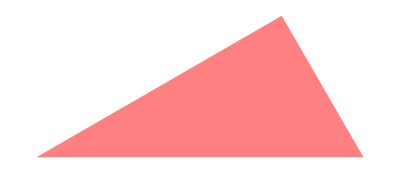
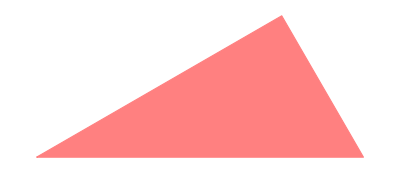
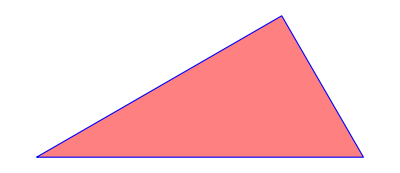
-Graphics- | Graphics[{RGBColor[1, 0.5, 0.5], Triangle[{{0, 0}, {2, 0}, {3/2, Sqrt[3]/2}}]}] | Graphics: LightPink Triangle.
-Graphics- | Graphics[{EdgeForm[Thickness[Large]], RGBColor[1, 0.5, 0.5], Triangle[{{0, 0}, {2, 0}, {3/2, Sqrt[3]/2}}]}] | Graphics: LightPink Triangle.
-Graphics- | Graphics[{EdgeForm[Dashing[{Small, Small}]], RGBColor[1, 0.5, 0.5], Triangle[{{0, 0}, {2, 0}, {3/2, Sqrt[3]/2}}]}] | Graphics: LightPink Triangle.
-Graphics- | Graphics[{EdgeForm[Directive[Thickness[Large], Dashing[{Small, Small}], RGBColor[0, 0, 1]]], RGBColor[1, 0.5, 0.5], Triangle[{{0, 0}, {2, 0}, {3/2, Sqrt[3]/2}}]}] | Graphics: LightPink Triangle.

```mathematica
aasTriangleTests={#,InputForm@#,Description@#}&/@aasTriangles;
Grid[aasTriangleTests,Frame->All]
```

ASATriangle

```mathematica
ℛ=ASATriangle[Pi/6,1,Pi/3];
asaTriangles={Graphics[{Pink,ℛ}],Graphics[{EdgeForm[Thick],Pink,ℛ}],Graphics[{EdgeForm[Dashed],Pink,ℛ}],Graphics[{EdgeForm[Directive[Thick,Dashed,Blue]],Pink,ℛ}]};
```

```mathematica
asaTriangleTests={#,InputForm@#,Description@#}&/@asaTriangles;
Grid[asaTriangleTests,Frame->All]
```

-Graphics- | Graphics[{RGBColor[1, 0.5, 0.5], Triangle[{{0, 0}, {1, 0}, {3/4, Sqrt[3]/4}}]}] | Graphics: LightPink Triangle.
-Graphics- | Graphics[{EdgeForm[Thickness[Large]], RGBColor[1, 0.5, 0.5], Triangle[{{0, 0}, {1, 0}, {3/4, Sqrt[3]/4}}]}] | Graphics: LightPink Triangle.
-Graphics- | Graphics[{EdgeForm[Dashing[{Small, Small}]], RGBColor[1, 0.5, 0.5], Triangle[{{0, 0}, {1, 0}, {3/4, Sqrt[3]/4}}]}] | Graphics: LightPink Triangle.
-Graphics- | Graphics[{EdgeForm[Directive[Thickness[Large], Dashing[{Small, Small}], RGBColor[0, 0, 1]]], RGBColor[1, 0.5, 0.5], Triangle[{{0, 0}, {1, 0}, {3/4, Sqrt[3]/4}}]}] | Graphics: LightPink Triangle.

AffineHalfSpace

```mathematica
affineHalfSpace=Graphics[{Red,AffineHalfSpace[{0,0},{{1,-1}},{1,1}]}];
```

```mathematica
affineHalfSpaceTest={affineHalfSpace,InputForm@affineHalfSpace,Description@affineHalfSpace}
Grid[{affineHalfSpaceTest},Frame->All]
```

{-Graphics-,Graphics[{RGBColor[1, 0, 0], AffineHalfSpace[{0, 0}, {{1, -1}}, {1, 1}]}],Graphics: Red AffineHalfSpace.}

-Graphics- | Graphics[{RGBColor[1, 0, 0], AffineHalfSpace[{0, 0}, {{1, -1}}, {1, 1}]}] | Graphics: Red AffineHalfSpace.

```mathematica
graphicsSymbols
```

{AASTriangle,ASATriangle,AffineHalfSpace,AffineSpace,Annulus,Arrow,BSplineCurve,Ball,BezierCurve,CapsuleShape,Circle,Circumsphere,Cone,ConicHullRegion,Cube,Cuboid,Cylinder,DiskSegment,Dodecahedron,Ellipsoid,EmptyRegion,FilledCurve,FullRegion,GraphicsComplex,HalfLine,HalfPlane,HalfSpace,Hexahedron,Hyperplane,Icosahedron,InfiniteLine,InfinitePlane,Insphere,JoinedCurve,Octahedron,Parallelepiped,Parallelogram,Polyhedron,Prism,Rectangle,RegularPolygon,SASTriangle,SSSTriangle,ShellRegion,Simplex,Sphere,SphericalShell,StadiumShape,Tetrahedron,Triangle,Tube}

```mathematica
EntityValue[Entity["WolframLanguageSymbol","AffineSpace"],EntityProperty["WolframLanguageSymbol","DocumentationBasicExamples"]]
```

AffineSpace

```mathematica
affineSpace=Graphics[{Green,AffineSpace[{0,0},{{1,-1}}]}];
```

```mathematica
affineSpaceTest={affineSpace,InputForm@affineSpace,Description@affineSpace};
Grid[{affineSpaceTest},Frame->All]
```

-Graphics- | Graphics[{RGBColor[0, 1, 0], AffineSpace[{0, 0}, {{1, -1}}]}] | Graphics: LightGreen AffineSpace.

## Keywords

<Keyword1>

Keyword2

....

## Acknowledgment

Mentor: <Mentor first name and last name>

<text>

## References

<Ref1>

<Ref2>

...